# Aggregate all cMUP data (ValScan, GlyScan, SlowChip)

```mathematica
notebookVersion=2.0;

keysUsed={"MutantID","ExpIndex","ManualGFPFlag","UniqueExptID","ChipType","LocalBackgroundRatio","Indices","EnzymeConc","fit_mm_datapoints","fit_mm_curved_r2","fit_mm_kcat","fit_mm_KM","fit_mm_scale_factor","FitR2","DataPoints","kcat","Km","ScaleFactor","SubstrateConc","OptLinFitSlope","OptLinFitSlopeMinusTrueBackground","kcat/Km","AllLBRs","AllInitialRates","AllSubstrateConcs","fit_mm_kcat_param_error","fit_mm_KM_param_error","fit_mm_kcatoverKM_MMfit","ContaminantRatio","AllEnzymeConcs"};

(* modified median function to return value if length of list = 1 *)
median2[x_]:=If[Length[x]==0,Median[{x}],Median[x]]
standardDeviation2[x_]:=If[Length[x]<2,"",StandardDeviation[x]];

twoPointCutoff=6;

rSqaredCutoff=0.97;

calcRatio[indices_,Sconc_]:=Module[{repeatRate,initRate},

initRate=allGrouped[indices][Select[#AssayType==1&&#SubstrateConc==Sconc&]][1,"OptLinFitSlope"];

repeatRate=allGrouped[indices][Select[#AssayType==0&]][1,"OptLinFitSlope"];

repeatRate/initRate]

generateDatasetFromCSV[in_,type_,id_,keysToTake_:keysUsed]:=Module[{dsIn,keys},

dsIn=in;

keys=dsIn[[1]];

r2key=Select[keysToTake,StringContainsQ[#,"curved_r2"]&][[1]];
dataPointsKey=Select[keysToTake,StringContainsQ[#,"datapoints"]&][[1]];

kcatKey=Select[keysToTake,StringContainsQ[#,"_kcat"]&][[1]];
kcatKmKey=Select[keysToTake,StringContainsQ[#,"_kcatover"]&][[1]];
KmKey=Select[keysToTake,StringContainsQ[#,"_KM"]&][[1]];
kcatUncorrected=kcatKey;
scaleFactorKey=Select[keysToTake,StringContainsQ[#,"scale_factor"]&][[1]];

all=Dataset[Table[Append[Association[Table[{keys[[n]]->dsIn[[i+1,n]]},{n,1,Length[keys]}]],{"ChipType"->type,"UniqueExptID"->id}],{i,1,Length[dsIn]-1}]];

repeatSconc=allGrouped[1][Select[#AssayType==0&]][1,"SubstrateConc"];

allGrouped=all[GroupBy["Indices"]];

all2=all[All,Append[#,{"FitR2"->#[r2key],"DataPoints"->#[dataPointsKey],"kcat"->#[kcatKey],"Km"->#[KmKey],"kcat/Km"->#[kcatKmKey],"ScaleFactor"->#[scaleFactorKey],"AllLBRs"->Normal[allGrouped[#Indices][All,"LocalBackgroundRatio"]],"AllInitialRates"->Normal[allGrouped[#Indices][All,"OptLinFitSlopeMinusTrueBackground"]],"AllSubstrateConcs"->Normal[allGrouped[#Indices][All,"SubstrateConc"]],"AllEnzymeConcs"->Normal[allGrouped[#Indices][All,"EnzymeConc"]]}]&];

all2[All,keysToTake]

]

(* function for remapping mutants with eGFP mutations and biomek errors *)

remapNames[dataset_]:=Module[{replaced1,replaced2,newDs},

remappingRules={"P76G"->"P92G","H172G"->"I188G*","T268G"->"D284G","A364G"->"M380G","N460G"->"L476G","T84V"->"D101V","T189V"->"N206V","G289V"->"G308V","I393V"->"D411V","P497V"->"P513V","H486E"->"H353E"};

(* addding M288V - spurious mutant, only a few reps in the MecMUP experiments *)

addFlags={"P448V"->"P448V*","Q131V"->"Q131V*","T425G"->"T425G*","N205G"->"N205G*","Y192G"->"Y192G*","G289V"->"G289V*","I188G"->"I188G*","M288V"->"M288V*"};

dsToAssociation=Normal[dataset];

replaced1=Fold[Replace[#1,#2,Infinity]&,dsToAssociation,remappingRules];

replaced2=Fold[Replace[#1,#2,Infinity]&,replaced1,addFlags];

newDs=Dataset[replaced2];

newDs[All,Append[#,"KnownBadMutant"->If[MemberQ[addFlags[[All,2]],#MutantID],1,0]]&]

]

(* removed R2 flags *)

cullBadChambers[dataset_]:=Module[{grouped,countFitPoints,twoPointFits},

(*dataset[Select[#ExpIndex==1&&#EnzymeConc>0.3&&#ManualGFPFlag==0&&#LocalBackgroundRatio>10.0&&#["FitR2"]>0.98&&MemberQ[twoPointFits,ToExpression[#Indices]]==False&]]*)

maxSubstrateConc=Max[dataset[1,"AllSubstrateConcs"]];

dataset[Select[(#SubstrateConc==maxSubstrateConc||#SubstrateConc==Round[maxSubstrateConc])&&#EnzymeConc>0.3&&#ManualGFPFlag==0&&#LocalBackgroundRatio>5.0&&#ContaminantRatio>5.0&&(#["kcat/Km"]>0.001&&#["kcat/Km"]<10000.0)&]]

]

cullExpressors[dataset_]:=Module[{grouped,countFitPoints,twoPointFits},

(*dataset[Select[#ExpIndex==1&&#EnzymeConc>0.3&&#ManualGFPFlag==0&&#LocalBackgroundRatio>10.0&&#["FitR2"]>0.98&&MemberQ[twoPointFits,ToExpression[#Indices]]==False&]]*)

(*dataset[Select[(#SubstrateConc==SconcToCullOn||#SubstrateConc==Round[SconcToCullOn])&&(#LocalBackgroundRatio≤5.0||#["FitR2"]≤0.97)&&#EnzymeConc>0.3&&#ManualGFPFlag==0&]]*)

maxSubstrateConc=Max[dataset[1,"AllSubstrateConcs"]];

(* removed fitR2 flag *)
dataset[Select[(#SubstrateConc==maxSubstrateConc||#SubstrateConc==Round[maxSubstrateConc])&&(#LocalBackgroundRatio≤5.0||#ContaminantRatio≤5.0||#["kcat/Km"]≤0||#FitR2≤0)&&#EnzymeConc>0.3&&#ManualGFPFlag==0&]]

]
```

#### Import all Michaelis-Menten data (1 csv per experiment):

For each individual experiment, the CSV file is imported and then the following functions are applied sequentially:

1. 'generateDatasetFromCSV' - converts CSV "Table" format into Dataset format. I'm also appending the chip type (e.g. GlyScan) and the filename in order to ensure that each experiment contains a unique identifier string.

2. 'cullBadChambers' - this function groups the data by chamber and applies our standard QC criteria as selection criteria, removing those chambers that are bad/low-quality.

```mathematica
files={{"/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/180528_S2_d2_MecMUP_1_MecMUP_LinComb.csv.bz2","ValScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/180402_S3_d2_MecMUP_1_MecMUP_LinComb.csv.bz2","ValScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv.bz2","GlyScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv.bz2","GlyScan"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv.bz2","GlyScan"},

{"/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/190804_S2_d1_MecMUP_1_MecMUP_LinComb.csv.bz2","SlowChip"},

{"/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/191128_S2_d3_MecMUP_1_MecMUP_LinComb.csv.bz2","SlowestChip"},
{"/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/191208_S2_d3_MecMUP_1_MecMUP_LinComb.csv.bz2","SlowestChip"}
};

inputFilePaths=files[[All,1]]

scanType=files[[All,2]]
```

{/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/180528_S2_d2_MecMUP_1_MecMUP_LinComb.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/180402_S3_d2_MecMUP_1_MecMUP_LinComb.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/190804_S2_d1_MecMUP_1_MecMUP_LinComb.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/191128_S2_d3_MecMUP_1_MecMUP_LinComb.csv.bz2,/Users/craig/Dropbox/HTMEK_processing/final_data/MecMUP/per-experiment_csvs/191208_S2_d3_MecMUP_1_MecMUP_LinComb.csv.bz2}

{ValScan,ValScan,GlyScan,GlyScan,GlyScan,SlowChip,SlowestChip,SlowestChip}

Note: Need the append below for a single SlowChip experiment for which I need to change some keys:

```mathematica
ProgressIndicator[Dynamic[itr],{1,Length[inputFilePaths]}]

pathLengthToDrop={76,76,76,76,76,76,76,76};

datasets=Table[remapNames[generateDatasetFromCSV[Import[inputFilePaths[[itr]],"Data"],scanType[[itr]],StringDrop[StringDrop[inputFilePaths[[itr]],-4],pathLengthToDrop[[itr]]]]],{itr,1,Length[inputFilePaths]}];

culledWithLigands=Join@@Table[cullBadChambers[datasets[[itr]]],{itr,1,Length[inputFilePaths]}];

culledIn=culledWithLigands[Select[(StringTake[#MutantID,-1]=="V"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="V"))||(StringTake[#MutantID,-1]=="G"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="G"))||#MutantID=="WT"||#MutantID=="R164A"||#MutantID=="K162A"||#MutantID=="N100A/R164A"||#MutantID=="T79G"||#MutantID=="T79S"||#MutantID=="N100A"&]];
```

```mathematica
slowWithLigands=Join@@Table[cullExpressors[datasets[[itr]]],{itr,1,Length[inputFilePaths]}];

slowIn=slowWithLigands[Select[(StringTake[#MutantID,-1]=="V"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="V"))||(StringTake[#MutantID,-1]=="G"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="G"))||#MutantID=="WT"||#MutantID=="R164A"||#MutantID=="K162A"||#MutantID=="N100A/R164A"||#MutantID=="T79G"||#MutantID=="T79S"||#MutantID=="N100A"&]];
```

```mathematica
unmeasuredIn=Complement[Normal[DeleteDuplicates[slowIn[All,"MutantID"]]],Normal[DeleteDuplicates[culledIn[All,"MutantID"]]]];
```

Group the aggregate dataset by mutant and print out a list of the experimental ID strings (for fast chips only):

```mathematica
groupedbyMutantInFastChips=culledIn[Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]][GroupBy["MutantID"]];

groupedbyMutantIn2FastChips=KeySortBy[groupedbyMutantInFastChips,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowInFastChips=slowIn[Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]][GroupBy["MutantID"]];

tooSlowIn2FastChips=KeySortBy[tooSlowInFastChips,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

(* SlowChip *)

groupedbyMutantInSlowChip=culledIn[Select[#ChipType=="SlowChip"&]][GroupBy["MutantID"]];

groupedbyMutantIn2SlowChip=KeySortBy[groupedbyMutantInSlowChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowInSlowChip=slowIn[Select[#ChipType=="SlowChip"&]][GroupBy["MutantID"]];

tooSlowIn2SlowChip=KeySortBy[tooSlowInSlowChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&]

(* SlowestChip *)

groupedbyMutantInSlowestChip=culledIn[Select[#ChipType=="SlowestChip"&]][GroupBy["MutantID"]];

groupedbyMutantIn2SlowestChip=KeySortBy[groupedbyMutantInSlowestChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowInSlowestChip=slowIn[Select[#ChipType=="SlowestChip"&]][GroupBy["MutantID"]];

tooSlowIn2SlowestChip=KeySortBy[tooSlowInSlowestChip,ToExpression[StringDrop[StringDrop[#,1],-1]]&]
```

Dataset[<>]

Dataset[<>]

Perform additional culling step on mutants for which only 1-2 of many replicates passed culling.

Using a higher threshold for the SlowestChip data, as this has skipped chambers and the background dynamic range is much lower.

```mathematica
Dynamic[mutant]

cutoffThreshold=0.6;

cutoffThresholdSlowest=1.0;

cullTableFast=Table[Clear[lbrs,fractionCulled];
lbrs=Table[Normal[groupedbyMutantIn2FastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutantIn2FastChips[mutant]]}];
fractionCulled=N[1-Length[lbrs]/(Length[lbrs]+If[MissingQ[tooSlowIn2FastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInFastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])];
{groupedbyMutantIn2FastChips[mutant,1,"MutantID"],fractionCulled,"FastChip",(Length[lbrs]+If[MissingQ[tooSlowIn2FastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInFastChips[groupedbyMutantIn2FastChips[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])}

,{mutant,1,Length[groupedbyMutantIn2FastChips]}];

cullTableSlow=Table[Clear[lbrs,fractionCulled];
lbrs=Table[Normal[groupedbyMutantIn2SlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutantIn2SlowChip[mutant]]}];
fractionCulled=N[1-Length[lbrs]/(Length[lbrs]+If[MissingQ[tooSlowIn2SlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])];
{groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],fractionCulled,"SlowChip",(Length[lbrs]+If[MissingQ[tooSlowIn2SlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowChip[groupedbyMutantIn2SlowChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])}

,{mutant,1,Length[groupedbyMutantIn2SlowChip]}];

cullTableSlowest=Table[Clear[lbrs,fractionCulled];
lbrs=Table[Normal[groupedbyMutantIn2SlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutantIn2SlowestChip[mutant]]}];
fractionCulled=N[1-Length[lbrs]/(Length[lbrs]+If[MissingQ[tooSlowIn2SlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])];
{groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],fractionCulled,"SlowChip",(Length[lbrs]+If[MissingQ[tooSlowIn2SlowChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],1,"LocalBackgroundRatio"]],0,Length[tooSlowInSlowestChip[groupedbyMutantIn2SlowestChip[mutant,1,"MutantID"],All,"LocalBackgroundRatio"]]])}

,{mutant,1,Length[groupedbyMutantIn2SlowestChip]}];

passedCullingFast=Select[cullTableFast,#[[2]]>cutoffThreshold&]
passedCullingSlow=Select[cullTableSlow,#[[2]]>cutoffThreshold&]
passedCullingSlowest=Select[cullTableSlowest,#[[2]]>cutoffThresholdSlowest&]
```

{{P29V,0.75,FastChip,4},{D38G,0.777778,FastChip,9},{Q39G,0.666667,FastChip,6},{R41V,0.75,FastChip,4},{D43G,0.833333,FastChip,6},{Y46G,0.666667,FastChip,6},{Y48G,0.666667,FastChip,6},{Y48V,0.833333,FastChip,6},{Y52G,0.666667,FastChip,6},{G53V,0.75,FastChip,4},{R59G,0.833333,FastChip,6},{G64A,0.666667,FastChip,6},{N68V,0.666667,FastChip,3},{V75G,0.8,FastChip,5},{V91G,0.833333,FastChip,6},{D104V,0.666667,FastChip,3},{V122G,0.8,FastChip,5},{D144G,0.833333,FastChip,6},{L148G,0.666667,FastChip,6},{V156G,0.666667,FastChip,6},{D163V,0.75,FastChip,4},{H172V,0.666667,FastChip,3},{N173V,0.666667,FastChip,3},{G176V,0.666667,FastChip,3},{T189G,0.833333,FastChip,6},{Y193V,0.75,FastChip,4},{V201G,0.833333,FastChip,6},{K207V,0.666667,FastChip,6},{W218G,0.666667,FastChip,6},{F249G,0.833333,FastChip,6},{K256V,0.75,FastChip,4},{D292V,0.666667,FastChip,3},{F296V,0.75,FastChip,4},{G308V,0.9,FastChip,10},{I316G,0.833333,FastChip,6},{E317G,0.8,FastChip,5},{D320G,0.833333,FastChip,6},{A351G,0.833333,FastChip,6},{A351V,0.75,FastChip,4},{A355V,0.666667,FastChip,3},{M362G,0.666667,FastChip,6},{M362V,0.75,FastChip,4},{M367G,0.833333,FastChip,6},{F388G,0.666667,FastChip,6},{N399V,0.666667,FastChip,3},{Q401V,0.75,FastChip,4},{Y403G,0.8,FastChip,5},{L416G,0.666667,FastChip,6},{R420V,0.75,FastChip,4},{S432V,0.666667,FastChip,6},{V433G,0.666667,FastChip,6},{Y435V,0.75,FastChip,4},{T439G,0.666667,FastChip,6},{I442G,0.833333,FastChip,6},{R454V,0.75,FastChip,4},{I456G,0.833333,FastChip,6},{N457V,0.666667,FastChip,3},{G458V,0.875,FastChip,8},{R463G,0.833333,FastChip,6},{G465A,0.666667,FastChip,6},{I470G,0.833333,FastChip,6},{G474V,0.666667,FastChip,3},{Y475G,0.666667,FastChip,6},{S477V,0.666667,FastChip,3},{T485V,0.666667,FastChip,3},{S487V,0.75,FastChip,4},{W489V,0.666667,FastChip,3},{Y492V,0.625,FastChip,8},{S494V,0.75,FastChip,4},{P497G,0.833333,FastChip,6},{F500V,0.666667,FastChip,3},{M501V,0.666667,FastChip,3},{G504V,0.75,FastChip,4},{G508V,0.75,FastChip,4},{S510V,0.666667,FastChip,3},{Y514G,0.833333,FastChip,6},{T517G,0.666667,FastChip,6},{K528V,0.666667,FastChip,3},{I529G,0.833333,FastChip,6}}

{{P29G,0.75,SlowChip,4},{R59G,0.666667,SlowChip,3},{G64A,0.75,SlowChip,4},{G82A,0.666667,SlowChip,6},{N100G,0.8,SlowChip,5},{N100V,0.666667,SlowChip,6},{L146G,0.833333,SlowChip,6},{F187G,0.666667,SlowChip,3},{M288G,0.75,SlowChip,4},{D295V,0.666667,SlowChip,3},{D352G,0.75,SlowChip,4},{I451G,0.75,SlowChip,4},{I519G,0.666667,SlowChip,3},{L527G,0.75,SlowChip,4}}

{}

```mathematica
unmeasuredIn
unmeasuredFast=passedCullingFast[[All,1]]
unmeasuredSlow=passedCullingSlow[[All,1]]
unmeasuredSlowest=passedCullingSlowest[[All,1]]
```

{A165V,A520V,D116G,D116V,D144V,D305G,D305V,D326G,D326V,D337G,D337V,D352V,D38V,D518V,F152V,F178G,F187V,F204G,F332G,F333G,F348G,F500G,F57G,G171V,G312V,G34V,G354V,G370V,G465V,G502A,G502V,G537A,G537V,G56V,G64V,G82V,G89V,G96V,H309G,H309V,H486G,H486V,H495G,H495V,H95G,I167G,I283G,I442V,I447G,I496G,I505G,I540G,I72G,I94G,I97G,K155V,K452V,K472V,L168G,L264V,L274G,L276G,L297G,L301G,L31G,L323G,L325G,L329G,L336G,L349G,L349V,L35G,M278G,M40V,N100A,N100A/R164A,N151G,N216V,N272V,N344V,N460V,P169V,P448G,P532V,P76V,P92V,Q386G,Q39V,R454G,S133V,S160V,S190V,S464V,S533V,S90V,S93V,T191V,T246G,T304V,T522G,T79G,T79V,V299G,V340G,V523G,V70G,V78A,V78G,W102G,W102V,W179G,W179V,W200G,W200V,Y192V,Y193G,Y322G,Y345G,Y435G,Y459G}

{P29V,D38G,Q39G,R41V,D43G,Y46G,Y48G,Y48V,Y52G,G53V,R59G,G64A,N68V,V75G,V91G,D104V,V122G,D144G,L148G,V156G,D163V,H172V,N173V,G176V,T189G,Y193V,V201G,K207V,W218G,F249G,K256V,D292V,F296V,G308V,I316G,E317G,D320G,A351G,A351V,A355V,M362G,M362V,M367G,F388G,N399V,Q401V,Y403G,L416G,R420V,S432V,V433G,Y435V,T439G,I442G,R454V,I456G,N457V,G458V,R463G,G465A,I470G,G474V,Y475G,S477V,T485V,S487V,W489V,Y492V,S494V,P497G,F500V,M501V,G504V,G508V,S510V,Y514G,T517G,K528V,I529G}

{P29G,R59G,G64A,G82A,N100G,N100V,L146G,F187G,M288G,D295V,D352G,I451G,I519G,L527G}

{}

```mathematica
(* selecting chambers that have been identified as containing too many culled replicates, excepting those that have a second-order LBR >5 *)
slowPassedFastChip=culledIn[Select[MemberQ[passedCullingFast[[All,1]],#MutantID]&&(#ChipType=="GlyScan"||#ChipType=="ValScan")&]];
slowPassedSlowChip=culledIn[Select[MemberQ[passedCullingSlow[[All,1]],#MutantID]&&(#ChipType=="SlowChip")&]];
slowPassedSlowestChip=culledIn[Select[MemberQ[passedCullingSlowest[[All,1]],#MutantID]&&(#ChipType=="SlowestChip")&]];

(* take Fast data that didn't meet criterion above - note here I'm selecting based on entire row, not just mutant ID *)
culledFast=culledIn[Select[MemberQ[slowPassedFastChip,#]==False&]];

(* take Slow data that didn't meet criterion above - same as above except operating on culledFast *)
culledSlow=culledFast[Select[MemberQ[slowPassedSlowChip,#]==False&]];

(* take Slowest data that didn't meet criterion above - same as above except operating on culledSlow *)
culledSlowest=culledSlow[Select[MemberQ[slowPassedSlowestChip,#]==False&]]

slow=Join[slowPassedFastChip,slowPassedSlowChip,slowPassedSlowestChip,slowIn];

culled=culledSlowest;
```

Dataset[<>]

```mathematica
groupedbyMutantIn=culled[GroupBy["MutantID"]];

groupedbyMutant=KeySortBy[groupedbyMutantIn,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

tooSlowIn=slow[GroupBy["MutantID"]];

tooSlow=KeySortBy[tooSlowIn,ToExpression[StringDrop[StringDrop[#,1],-1]]&];

datasetsIn=DeleteDuplicates[Flatten[Values[Normal[groupedbyMutant[All,All,"UniqueExptID"]]]]]
```

{180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv,180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv,180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv,180528_S2_d2_MecMUP_1_MecMUP_LinComb.csv,180402_S3_d2_MecMUP_1_MecMUP_LinComb.csv,190804_S2_d1_MecMUP_1_MecMUP_LinComb.csv,191208_S2_d3_MecMUP_1_MecMUP_LinComb.csv,191128_S2_d3_MecMUP_1_MecMUP_LinComb.csv}

```mathematica
Print["Length of aggregate data set (number of unique measurements)"];
Length[culled]

mutantsWithData=Sort[DeleteDuplicates[Normal[culled[All,"MutantID"]]],ToExpression[StringDrop[StringDrop[#1,-1],1]]<ToExpression[StringDrop[StringDrop[#2,-1],1]]&];

Print["Number of total mutants with at least 1 Michaelis-Menten curve:"];
Length[mutantsWithData]

Print["Mutants too slow to have at least 1 culled measurement:"]
unmeasured=Complement[Normal[DeleteDuplicates[slow[All,"MutantID"]]],Normal[DeleteDuplicates[culled[All,"MutantID"]]]]

countRepsCulled=culled[Select[(StringTake[#MutantID,-1]=="V"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="V"))||(StringTake[#MutantID,-1]=="G"||(StringTake[#MutantID,-1]=="A"&&StringTake[#MutantID,1]=="G"))&]][GroupBy["MutantID"]];

Print["Table of number of replicates per mutant:"]
Sort[Length[#]&/@countRepsCulled]

Print["Mean number of replicates per mutant:"]
N[Mean[Values[Normal[(Length[#]&/@countRepsCulled)]]]]
```

Length of aggregate data set (number of unique measurements)

4867

Number of total mutants with at least 1 Michaelis-Menten curve:

861

Mutants too slow to have at least 1 culled measurement:

{A165V,A351G,A351V,A355V,A520V,D104V,D116G,D116V,D144G,D144V,D292V,D295V,D305G,D305V,D326G,D326V,D337G,D337V,D352V,D38V,D518V,F152V,F178G,F187G,F187V,F204G,F296V,F332G,F333G,F348G,F388G,F500G,F500V,F57G,G171V,G176V,G308V,G312V,G34V,G354V,G370V,G465V,G474V,G502A,G502V,G504V,G537A,G537V,G53V,G56V,G64A,G64V,G82V,G89V,G96V,H172V,H309G,H309V,H486G,H486V,H495G,H495V,H95G,I167G,I283G,I316G,I442G,I442V,I447G,I496G,I505G,I519G,I540G,I72G,I94G,I97G,K155V,K207V,K256V,K452V,K472V,K528V,L146G,L148G,L168G,L264V,L274G,L276G,L297G,L301G,L31G,L323G,L325G,L329G,L336G,L349G,L349V,L35G,L416G,L527G,M278G,M288G,M362G,M362V,M40V,M501V,N100A,N100A/R164A,N100V,N151G,N173V,N216V,N272V,N344V,N399V,N460V,N68V,P169V,P29G,P29V,P448G,P497G,P532V,P76V,P92V,Q386G,Q39V,Q401V,R41V,R420V,R454G,R454V,R59G,S133V,S160V,S190V,S432V,S464V,S477V,S487V,S510V,S533V,S90V,S93V,T191V,T246G,T304V,T485V,T517G,T522G,T79G,T79V,V156G,V299G,V340G,V523G,V70G,V75G,V78A,V78G,V91G,W102G,W102V,W179G,W179V,W200G,W200V,W489V,Y192V,Y193G,Y193V,Y322G,Y345G,Y403G,Y435G,Y459G,Y46G,Y48V,Y492V,Y514G}

Table of number of replicates per mutant:

Mean number of replicates per mutant:

4.54026

#### Input parameters:

Parameters below define which "keys" we're interested in using and aggregating:

```mathematica
kcatKmKey="kcat/Km";

kcatKey="kcat";
KmKey="Km";
kcatUncorrected="kcat";
(*VmaxKey="VmaxMMfit optlin PerPointScaled";*)
scaleFactorKey="ScaleFactor";

numStatsBootstraps=10000;

numBootstraps=5;

(*KiFitCutoff=10000.0;*)
kcatFitCutoff=10000.0;
KmCutoff=10000.0;
```

#### Normalization to internal WT parameters (kcat/Km):

Chip-to-chip differences, for example the intrinsic variability of flow through the device, or the length of time the enzyme has been sitting on the button, influence the fractional activity of enzyme mutants across the device. In the first example, increased wait times before beginning an assay result in some fraction of activity loss due to enzyme "death", while flow issues can influence the effectiveness of the SDS wash. In both these cases, the fitted kcat values will vary modestly between chips.

Given these known issues, we can normalize the kcat values from each experimental dataset based on the subset of WT mutants on each chip. This removes any systematic, global (on the experimental level).

```mathematica
datasetsIn=DeleteDuplicates[Flatten[Values[Normal[groupedbyMutant[All,All,"UniqueExptID"]]]]];

(* for MecMUP, do not need to separate fast and slow/slowest chips as for cMUP/MeP-based assays *)
fastChips=datasetsIn;
(*slowChips=Select[datasetsIn,StringContainsQ[#,"Slow"]&];*)

groupedByExperimentWT=
groupedbyMutant["K162A"][All,
{"UniqueExptID",kcatKmKey}
][
GroupBy["UniqueExptID"]
];

fast=groupedByExperimentWT[fastChips]

(*groupedByExperimentR164A=
groupedbyMutant["R164A"][All,
{"UniqueExptID",kcatKey}
][
GroupBy["UniqueExptID"]
];
slow=groupedByExperimentR164A[slowChips];*)

Print["Below is the WT median for the fast chips only:"];
wtMedian=Median[(Join@@Values[Normal[fast[All,All,kcatKmKey]]])]

Print["Below are the per-chip normalization factors based on the WT median:"];
normalizationDataFast=Association[Table[fastChips[[n]]->If[NumberQ[(Median[Normal[fast[fastChips[[n]],All,kcatKmKey]]]/wtMedian)],Median[Normal[fast[fastChips[[n]],All,kcatKmKey]]]/wtMedian,1.0],{n,1,Length[fastChips]}]]

normalizationData=normalizationDataFast
```

Below is the WT median for the fast chips only:

37.0857

Below are the per-chip normalization factors based on the WT median:

<|180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv→0.957776,180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv→1.05382,180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv→0.875161,180528_S2_d2_MecMUP_1_MecMUP_LinComb.csv→1.33884,180402_S3_d2_MecMUP_1_MecMUP_LinComb.csv→0.820966,190804_S2_d1_MecMUP_1_MecMUP_LinComb.csv→0.613,191208_S2_d3_MecMUP_1_MecMUP_LinComb.csv→0.410246,191128_S2_d3_MecMUP_1_MecMUP_LinComb.csv→1.23947|>

<|180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv→0.957776,180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv→1.05382,180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv→0.875161,180528_S2_d2_MecMUP_1_MecMUP_LinComb.csv→1.33884,180402_S3_d2_MecMUP_1_MecMUP_LinComb.csv→0.820966,190804_S2_d1_MecMUP_1_MecMUP_LinComb.csv→0.613,191208_S2_d3_MecMUP_1_MecMUP_LinComb.csv→0.410246,191128_S2_d3_MecMUP_1_MecMUP_LinComb.csv→1.23947|>

#### Aggregating WT data across experiments, applying normalization factors:

Apply the calculated WT normalization factors to each dataset (on kcat) and plot histograms of the WT kcat values before and after this correction, to assess improvement:

{14.6532,13.9988,31.0724,14.7143,16.9225,19.9157,10.6318,11.3405,15.3376,21.6274,21.7973,14.72,14.7988,17.3568,14.9462,6.88545,8.2039,12.937,7.6895,10.1629,7.97855,7.05091,8.54728,11.9567,17.6028,8.48592,6.31444,11.0683,13.434,7.93388,8.91594,4.95492,5.39138,3.04895,23.2614,22.3871,21.9389,21.4569,21.6991,21.5879,14.0755,17.1591,19.4164,20.3293,16.5473,17.7908,16.3146,20.8423,18.4165,25.6393,19.1357,19.2396,18.5899,17.2171,14.2688,14.3288,22.2337,14.8087,12.7012,16.1726,17.1693,26.1322,15.2196,18.4459,22.3756,20.2297,11.8628,11.2492,9.28358,20.0432,10.9277,13.5695,26.2069,20.7873,20.3473,17.6238,20.3398,17.1812,23.7496,15.0732,21.0127,18.7711,24.0936,20.2361,15.4598,11.7927,10.6175,13.6697,15.5928,12.8756,12.5832,11.192,9.24261,9.31228}

15.3987

201161.

95% confidence bounds on fitted WT kcat and KM parameters:

{5.39138,26.1322}

{57571.9,287507.}

Aggregated K162A kcat values, before correction:

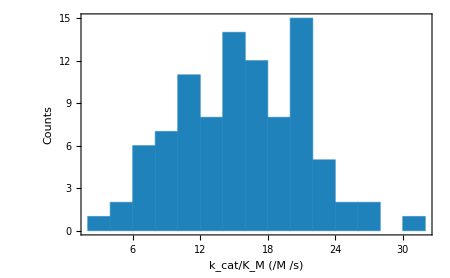

{6.56712,27.1374}

Aggregated kcat values, after correction:

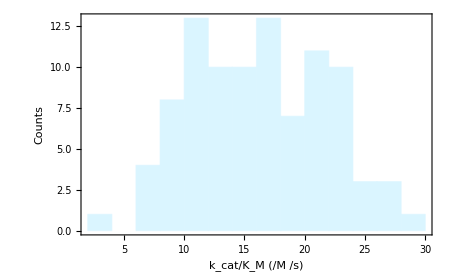

Aggregated kcat values, before and after correction overlaid:

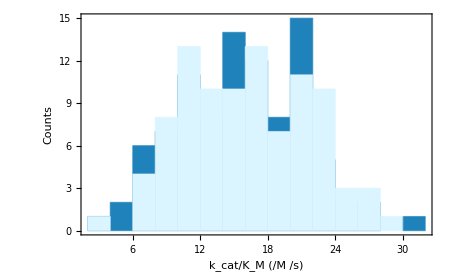

{7.86245,7.68497,15.9002,7.36188,8.78256,10.2868,5.7886,6.26638,8.68414,11.2479,10.4732,6.53212,6.42654,5.20151,5.73878,6.63996,8.23783,13.7538,7.88309,11.2176,8.17068,7.47684,8.25696,12.8367,17.0427,9.06701,6.41396,13.4284,14.745,7.90642,10.0564,3.96305,5.38199,1.80472,16.0567,14.2708,12.8257,13.0608,12.925,11.3212,8.44746,10.2594,11.4865,12.5247,8.94929,11.024,8.67125,10.5062,11.1376,13.8639,9.6181,11.5904,19.8736,17.8504,14.5612,15.3515,20.3662,15.5911,12.7353,17.7377,18.1531,16.5956,14.4978,18.7937,12.3383,11.8042,11.4432,6.7996,6.7904,13.8952,9.52264,12.8268,18.1121,13.9015,13.9558,12.7057,13.6612,12.9297,16.1597,11.8244,14.6642,14.1513,16.1938,12.6465,9.46658,6.35021,5.9949,8.85073,10.2831,7.84772,8.25477,7.03754,5.57245,4.16811}

```mathematica
normalizingMutant="WT";

allWTkcatKmValues=Normal[groupedbyMutant[normalizingMutant][All,kcatKmKey]]

allWTkcatValues=Normal[groupedbyMutant[normalizingMutant][All,kcatKey]];

allWTKmValues=Normal[groupedbyMutant[normalizingMutant][All,KmKey]];

wtMedian=Median[allWTkcatKmValues]

KmMedian=Median[Select[allWTKmValues,NumberQ[#]&]]

(* calculate 95% confidence bounds on both WT parameters *)
Print["95% confidence bounds on fitted WT kcat and KM parameters:"]
wtkcatCIs=Quantile[allWTkcatKmValues,{0.025,0.975}]
wtKmCIs=Quantile[Select[allWTKmValues,NumberQ[#]&],{0.025,0.975}]

(* plot distribution of WT Ki values *)
Print["Aggregated K162A kcat values, before correction:"]
histPreCorrection=Histogram[allWTkcatKmValues,{2.0},PlotRange->All,ChartStyle->ColorData[16,6],Frame->True,Axes->False,FrameStyle->Directive[Black,18],FrameLabel->{"k_cat/K_M (/M /s)","Counts"},ImageSize->450]

normalizedWTkcatKmvalues=Table[Normal[groupedbyMutant[normalizingMutant][n,kcatKmKey]]/normalizationData[Normal[groupedbyMutant[normalizingMutant,n,"UniqueExptID"]]],{n,1,Length[allWTkcatValues]}];

normalizedWTkcatvalues=Table[Normal[groupedbyMutant[normalizingMutant][n,kcatKey]]/normalizationData[Normal[groupedbyMutant[normalizingMutant,n,"UniqueExptID"]]],{n,1,Length[allWTkcatValues]}];

wtNormalizedkcatCIs=Quantile[normalizedWTkcatKmvalues,{0.025,0.975}]

Print["Aggregated kcat values, after correction:"]
histPostCorrection=Histogram[normalizedWTkcatKmvalues,{2.0},PlotRange->All,ChartStyle->ColorData[16,5],Frame->True,Axes->False,FrameStyle->Directive[Black,18],FrameLabel->{"k_cat/K_M (/M /s)","Counts"},ImageSize->450]

Print["Aggregated kcat values, before and after correction overlaid:"]
Show[histPreCorrection,histPostCorrection]

wtDataNormAll=Table[{normalizedWTkcatvalues[[n]],allWTKmValues[[n]],normalizedWTkcatKmvalues[[n]]},{n,1,Length[allWTkcatKmValues]}];

exptsWT=Table[Normal[groupedbyMutant[normalizingMutant,n,"UniqueExptID"]],{n,1,Length[groupedbyMutant["WT"]]}];
normalizationFactorsWT=normalizationData[#]&/@exptsWT;

enzymeConcsWT=Table[Normal[groupedbyMutant[normalizingMutant,n,"AllEnzymeConcs"]][[1]],{n,1,Length[groupedbyMutant["WT"]]}];

kobsExptIndex=1;

(* kobs determined by scaling linear fit at lowest [S] by [S] and [E] *)
kobsWT=Table[Normal[groupedbyMutant["WT",n,"AllInitialRates"][[kobsExptIndex]]]/(normalizationFactorsWT[[n]]*(Normal[groupedbyMutant["WT",n,"AllSubstrateConcs"][[kobsExptIndex]]])*enzymeConcsWT[[n]]*10^-9),{n,1,Length[groupedbyMutant["WT"]]}]

wtDataNormAll=Table[{normalizedWTkcatvalues[[n]],allWTKmValues[[n]],normalizedWTkcatvalues[[n]]/(allWTKmValues[[n]]*10^-6),kobsWT[[n]]},{n,1,Length[allWTkcatValues]}];
```

#### Generate an overlaid plot of the wild-type Michaelis-Menten fits for coplotting with mutant Michaelis-Menten fits, to aid interpretation of p-values:

Now want to look at the fitted WT Michaelis-Menten curves overlaid. Plotting all the individual curves in light gray, with the median curve overlaid in dark gray, and curves corresponding to the 99% confidence bounds shown as intermediate gray curves:

```mathematica
(*curves=Table[RandomChoice[normalizedWTkcatvalues]*RandomReal[NormalDistribution[1.0,0.01]]*sub/(RandomChoice[allWTKmValues]*RandomReal[NormalDistribution[1.0,0.01]]+sub),{n,1,200}];*)

curves=Table[normalizedWTkcatvalues[[n]]*sub/(allWTKmValues[[n]]+sub),{n,1,Length[normalizedWTkcatvalues]}];
curvesKm=Table[1.0*sub/(allWTKmValues[[n]]+sub),{n,1,Length[normalizedWTkcatvalues]}];
```

{1.61181,5.18024}

{151386.,262213.}

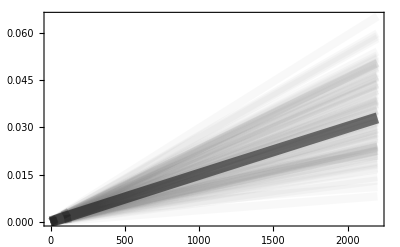

```mathematica
densityFilling1=Plot[curves,{sub,0,2200},PlotStyle->Directive[Gray,Thickness[0.015],Opacity[0.05]],PlotPoints->2,Frame->True,Axes->False];

kcatResampled=Quantile[Table[Median[RandomChoice[normalizedWTkcatvalues,5]],{526}],{0.01,0.99}]

KmResampled=Quantile[Table[Median[RandomChoice[allWTKmValues,5]],{526}],{0.01,0.99}]

densityFilling=Show[densityFilling1,Plot[Median[normalizedWTkcatvalues]*sub/(Median[allWTKmValues]+sub),{sub,0,2200},PlotRange->All,PlotStyle->Directive[Black,Thickness[0.02],Opacity[0.5]]],Plot[kcatResampled[[1]]*sub/(Median[allWTKmValues]+sub),{sub,0,150},PlotRange->All,PlotStyle->Directive[Black,Thickness[0.015],Dashed,Opacity[0.2]]],Plot[kcatResampled[[2]]*sub/(Median[allWTKmValues]+sub),{sub,0,150},PlotRange->All,PlotStyle->Directive[Black,Thickness[0.015],Dashed,Opacity[0.2]]]]

densityFillingKm=Plot[curvesKm,{sub,0,150},PlotStyle->Directive[Gray,Thickness[0.015],Opacity[0.02]],PlotPoints->2,Frame->True,Axes->False,PlotRange->{0,All}];
```

#### Some code to facilitate automatic plotting and legending (evaluate cell below):

Just lists of colors, plotmarkers, and dashing types, so that each experiment gets its own plot marker, color, and dashing type:

```mathematica
xticks={{{0.1,0},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{500,500},{5000,5000}},None};
xticks2={{{0.01,0},{0.1,0.1},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{500,500},{5000,5000}},None};

colorMap=Association[Table[datasetsIn[[n]]->ColorData[24,n-1],{n,1,Length[datasetsIn]}]]

plotMarkerList={●,○,◆,◇,■,□,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●,●};

dashingList={Dashing[None],Dashing[0.05],Dashing[0.015],Dashing[0.03],Dotted,Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None]};

dashingListLeg={Dashing[None],Dashing[0.05*5],Dashing[0.015*5],Dashing[0.03*5],Dotted,Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None]};
```

<|180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv→RGBColor[0.8941176470588236, 0.7098039215686275, 0.7490196078431373],180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv→RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv→RGBColor[1., 0.7215686274509804, 0.2196078431372549],180528_S2_d2_MecMUP_1_MecMUP_LinComb.csv→RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],180402_S3_d2_MecMUP_1_MecMUP_LinComb.csv→RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],190804_S2_d1_MecMUP_1_MecMUP_LinComb.csv→RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],191208_S2_d3_MecMUP_1_MecMUP_LinComb.csv→RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],191128_S2_d3_MecMUP_1_MecMUP_LinComb.csv→RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355]|>

```mathematica
expIndexAssociation=<|"180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv"->1,"180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv"->2,"180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv"->3,"180528_S2_d2_MecMUP_1_MecMUP_LinComb.csv"->4,"180402_S3_d2_MecMUP_1_MecMUP_LinComb.csv"->5,"190804_S2_d1_MecMUP_1_MecMUP_LinComb.csv"->6,"191128_S2_d3_MecMUP_1_MecMUP_LinComb.csv"->7,"191208_S2_d3_MecMUP_1_MecMUP_LinComb.csv"->8|>
```

<|180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv→1,180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv→2,180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv→3,180528_S2_d2_MecMUP_1_MecMUP_LinComb.csv→4,180402_S3_d2_MecMUP_1_MecMUP_LinComb.csv→5,190804_S2_d1_MecMUP_1_MecMUP_LinComb.csv→6,191128_S2_d3_MecMUP_1_MecMUP_LinComb.csv→7,191208_S2_d3_MecMUP_1_MecMUP_LinComb.csv→8|>

#### Bootstrap functions (for p-value calculation and parameter error estimates) (evaluate hidden cell below):

'bsMedian' returns p-values for the following parameters, in the same order: {kcat, KM, kcat/KM}

```mathematica
Needs["HypothesisTesting`"]

bsMedianIteration[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS},

wtRS=median2[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[wtIn]]];
mutRS=median2[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[mutantKIswithCIs]]];

tstar=Abs[mutRS-wtRS]

]

bsMedian[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS,checkpoint1,checkpoint2,checkpoint3},

weightedMean=median2[mutantKIswithCIs];

If[Head[weightedMean]==Median,Return[{Indeterminate,Indeterminate,Indeterminate,Indeterminate}];Continue[]];

weightedWTMean=median2[wtIn];

tobs=Abs[(weightedMean-weightedWTMean)];

tstar=Table[bsMedianIteration[mutantKIswithCIs,wtIn],{100}];

(* calculate for kcat, Km, and kcat/Km simultaneously for speed *)
checkpoint1=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/100*1.0,{n,1,4}];

If[checkpoint1[[1]]>0.1&&checkpoint1[[2]]>0.1&&checkpoint1[[3]]>0.1&&checkpoint1[[4]]>0.1,

Return[checkpoint1],

tstar=Table[bsMedianIteration[mutantKIswithCIs,wtIn],{1000}];

checkpoint2=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/1000*1.0,{n,1,4}];

If[checkpoint2[[1]]>0.01&&checkpoint2[[2]]>0.01&&checkpoint2[[3]]>0.01&&checkpoint2[[4]]>0.01,

Return[checkpoint2],

tstar=Table[bsMedianIteration[mutantKIswithCIs,wtIn],{numStatsBootstraps}];

checkpoint3=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/numStatsBootstraps*1.0,{n,1,4}];

Return[checkpoint3]]

];

]

bsMeanIteration[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS},

wtRS=Mean[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[wtIn]]];
mutRS=Mean[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[mutantKIswithCIs]]];

tstar=Abs[mutRS-wtRS]

]

bsMean[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS,checkpoint1,checkpoint2,checkpoint3},

weightedMean=Mean[mutantKIswithCIs];

weightedWTMean=Mean[wtIn];

tobs=Abs[(weightedMean-weightedWTMean)];

tstar=Table[bsMeanIteration[mutantKIswithCIs,wtIn],{100}];

(* calculate for kcat, Km, and kcat/Km simultaneously for speed *)
checkpoint1=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/100*1.0,{n,1,4}];

If[checkpoint1[[1]]>0.1&&checkpoint1[[2]]>0.1&&checkpoint1[[3]]>0.1&&checkpoint1[[4]]>0.1,

Return[checkpoint1],

tstar=Table[bsMeanIteration[mutantKIswithCIs,wtIn],{1000}];

checkpoint2=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/1000*1.0,{n,1,4}];

If[checkpoint2[[1]]>0.01&&checkpoint2[[2]]>0.01&&checkpoint2[[3]]>0.01&&checkpoint2[[4]]>0.01,

Return[checkpoint2],

tstar=Table[bsMeanIteration[mutantKIswithCIs,wtIn],{numStatsBootstraps}];

checkpoint3=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/numStatsBootstraps*1.0,{n,1,4}];

Return[checkpoint3]]

];

]

(* function for bootstrapping residuals - to get parameter estimate errors *)

bsResidual[fitModel_,numBootstraps_]:=Module[{model,data,residuals,bootstraps,concentrations,reshuffled,newData,newFit,newParams},

(* extract input experimental data from FittedModel *)
model=fitModel;
data=model["Data"];

(* extract residuals *)
residuals=model["FitResiduals"];

(* reshuffle residuals and bootstrap (looped) *)
bootstraps=Table[
concentrations=data[[All,1]];

reshuffled=RandomChoice[residuals,Length[residuals]];

newData=Table[{concentrations[[n]],model[concentrations[[n]]]+reshuffled[[n]]},{n,1,Length[concentrations]}];

newFit=NonlinearModelFit[newData,{Vmax*substrate/(KM+substrate),KM>0&&Vmax>0},{Vmax,KM},substrate];

newParams=newFit["BestFitParameters"];

{Vmax/.newParams,KM/.newParams},{numBootstraps}]

]

bsStdDevIteration[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS},

wtRS=StandardDeviation[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[wtIn]]];
mutRS=StandardDeviation[RandomChoice[Join[wtIn,mutantKIswithCIs],Length[mutantKIswithCIs]]];

tstar=Abs[mutRS-wtRS]

]

bsStdDev[mutantKIswithCIs_,wtIn_]:=Module[{sample,tobs,bs1,bs2,tstar,weightedMean,weightedWTMean,wtRS,mutRS,checkpoint1,checkpoint2,checkpoint3},

weightedMean=StandardDeviation[mutantKIswithCIs];

If[Head[weightedMean]==StandardDeviation,Return[{Indeterminate,Indeterminate,Indeterminate}];Continue[]];

weightedWTMean=StandardDeviation[wtIn];

tobs=Abs[(weightedMean-weightedWTMean)];

tstar=Table[bsStdDevIteration[mutantKIswithCIs,wtIn],{100}];

(* calculate for kcat, Km, and kcat/Km simultaneously for speed *)
checkpoint1=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/100*1.0,{n,1,3}];

If[checkpoint1[[1]]>0.1&&checkpoint1[[2]]>0.1&&checkpoint1[[3]]>0.1,

Return[checkpoint1],

tstar=Table[bsStdDevIteration[mutantKIswithCIs,wtIn],{1000}];

checkpoint2=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/1000*1.0,{n,1,3}];

If[checkpoint2[[1]]>0.01&&checkpoint2[[2]]>0.01&&checkpoint2[[3]]>0.01,

Return[checkpoint2],

tstar=Table[bsStdDevIteration[mutantKIswithCIs,wtIn],{numStatsBootstraps}];

checkpoint3=Table[Length[Select[tstar[[All,n]],#>tobs[[n]]&]]/numStatsBootstraps*1.0,{n,1,3}];

Return[checkpoint3]]

];

]

colorPVal[pvalue_,cutoff_]:=If[pvalue≠"N/A",Which[pvalue<cutoff&&pvalue≠0.,Style[ToString[pvalue],Bold,ColorData[20,8]],pvalue==0.,Style["<"<>ToString[1.0/numStatsBootstraps],Bold,ColorData[20,8]],pvalue≥cutoff,ToString[pvalue]],"N/A"]
```

#### Structure mapping function:

```mathematica
pafa=Import["/Users/craig/Documents/Biochemistry/Reference/Structures/5tj3.pdb",ColorFunction->Function[{x},Directive[GrayLevel[0.8],Opacity[0.7]]]];

seq=Import["/Users/craig/Documents/Biochemistry/Reference/Structures/5tj3.pdb","Sequence"];

seqJoined=Join@@{Table[{n+23,StringTake[seq[[1]],{n}]},{n,1,StringLength[seq[[1]]]}],Table[{n+374,StringTake[seq[[2]],{n}]},{n,1,StringLength[seq[[2]]]}]};

coords=Import["/Users/craig/Documents/Biochemistry/Reference/Structures/5tj3.pdb","ResidueCoordinates"];

pafaAS=Import["/Users/craig/Dropbox/HTMEK_processing/desktop_move_200110/pafa_active_site_wLigands.pdb",ColorFunction->Function[{x},GrayLevel[0.8]]];

joined=Join[coords[[1]],coords[[2]]];

coordsJoined=joined;

cAlphaAssociation=Join[AssociationThread[seqJoined[[All,1]],coordsJoined[[All,2]]],Association[{21->{2535.,-1901.6,5793.},22->{2535.,-1901.6,5793.},23->{2535.,-1901.6,5793.},373->{-1794.2,-2367.6,1819.9},374->{-1553.7,-2917.8999999999996,1116.},546->{568.5,-1399.9,5539.099999999999}}]];

makeStructureNice[res_,mutation_]:=Module[{test2},test2=ListPointPlot3D[Callout[{cAlphaAssociation[res]},Style[mutation,18,Black],{1895.1,-25.,3038.1}],PlotStyle->Directive[PointSize[0.05],Darker[Red]]];

If[mutation≠"WT",Show[pafa,pafaAS,test2,Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,1,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,2,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,3,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,4,1]],150]}],ViewPoint -> {0.06632417997547935, -6.105008189695307, -3.7111895933377492}/7, 
  ViewVertical -> {-0.6985872717587375, 0.712147563133245, 0.06943826077937733},ImageSize->500],Show[pafa,pafaAS,Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,1,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,2,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,3,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,4,1]],150]}],ViewPoint -> {0.06632417997547935, -6.105008189695307, -3.7111895933377492}/7, 
  ViewVertical -> {-0.6985872717587375, 0.712147563133245, 0.06943826077937733},ImageSize->500]]]

makeStructureNiceDM[res1_,res2_,mutation_]:=Module[{test2,test3},test2=ListPointPlot3D[Callout[{cAlphaAssociation[res1]},Style[mutation,18,Black],{1895.1,-25.,3038.1}],PlotStyle->Directive[PointSize[0.05],Darker[Red]]];

test3=ListPointPlot3D[{cAlphaAssociation[res2]},PlotStyle->Directive[PointSize[0.05],Darker[Red]]];

Show[pafa,pafaAS,test2,test3,Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,1,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,2,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,3,1]],150]}],Graphics3D[{Darker[Gray],Specularity[White,10],Sphere[coords[[3,4,1]],150]}],ViewPoint -> {0.06632417997547935, -6.105008189695307, -3.7111895933377492}/7, 
  ViewVertical -> {-0.6985872717587375, 0.712147563133245, 0.06943826077937733},ImageSize->500]]
```

#### Function for statistical analysis, make aggregate plots, and output a dataset with aggregate plots, kinetic parameters, p-values etc. (evaluate hidden cell below):

```mathematica
(* association containing expression numbers, applied to 1000uM [cMUP] only *)
allData=Join@@datasets;
highestSonly=allData[Select[#ExpIndex==1&]];
allGroupedByMutantFast=highestSonly[Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]][GroupBy["MutantID"]];
allGroupedByMutantSlow=highestSonly[Select[#ChipType=="SlowChip"&]][GroupBy["MutantID"]];
allGroupedByMutantSlowest=highestSonly[Select[#ChipType=="SlowestChip"&]][GroupBy["MutantID"]];

expressionDataFast=Association[Table[allGroupedByMutantFast[mut,1,"MutantID"]->{Length[allGroupedByMutantFast[mut]],Length[allGroupedByMutantFast[mut][Select[#EnzymeConc>0.3&]]],N[Length[allGroupedByMutantFast[mut][Select[#EnzymeConc>0.3&]]]/Length[allGroupedByMutantFast[mut]]],Normal[allGroupedByMutantFast[mut][All,"EnzymeConc"]]},{mut,1,Length[allGroupedByMutantFast]}]];

expressionDataSlow=Association[Table[allGroupedByMutantSlow[mut,1,"MutantID"]->{Length[allGroupedByMutantSlow[mut]],Length[allGroupedByMutantSlow[mut][Select[#EnzymeConc>0.3&]]],N[Length[allGroupedByMutantSlow[mut][Select[#EnzymeConc>0.3&]]]/Length[allGroupedByMutantSlow[mut]]],Normal[allGroupedByMutantSlow[mut][All,"EnzymeConc"]]},{mut,1,Length[allGroupedByMutantSlow]}]];

expressionDataSlowest=Association[Table[allGroupedByMutantSlowest[mut,1,"MutantID"]->{Length[allGroupedByMutantSlowest[mut]],Length[allGroupedByMutantSlowest[mut][Select[#EnzymeConc>0.3&]]],N[Length[allGroupedByMutantSlowest[mut][Select[#EnzymeConc>0.3&]]]/Length[allGroupedByMutantSlowest[mut]]],Normal[allGroupedByMutantSlowest[mut][All,"EnzymeConc"]]},{mut,1,Length[allGroupedByMutantSlowest]}]];

(* WT fast and slow chip data separated *)

sortedWTbyChipType=groupedbyMutant["WT"][All,{"UniqueExptID","ChipType",kcatKey,KmKey}][GroupBy["ChipType"]];

fastChipDataWT={#[[2]]/normalizationData[#[[1]]],#[[3]],(#[[2]]/normalizationData[#[[1]]])/((#[[3]])*10^-6)}&/@Values[Join[Normal[sortedWTbyChipType["GlyScan",All,{"UniqueExptID",kcatKey,KmKey}]],Normal[sortedWTbyChipType["ValScan",All,{"UniqueExptID",kcatKey,KmKey}]]]];

slowChipDataWT={#[[2]]/normalizationData[#[[1]]],#[[3]],(#[[2]]/normalizationData[#[[1]]])/((#[[3]])*10^-6)}&/@Values[Normal[sortedWTbyChipType["SlowChip",All,{"UniqueExptID",kcatKey,KmKey}]]];

(* no WT on Slowest Chip *)

(* determine the per-chip replacement value for negative kobs (limit) values *)
(* ALSO ADD INDEX of LOWEST [S] EXPT - important for MeP *)
groupedByExptSlowOnly=slow[GroupBy["UniqueExptID"]];

kobsLimitReplacementValues=Association[Table[groupedByExptSlowOnly[expt,1,"UniqueExptID"]->Median[Select[Table[Normal[groupedByExptSlowOnly[expt,n,"AllInitialRates"][[kobsExptIndex]]]/(normalizationData[groupedByExptSlowOnly[expt,1,"UniqueExptID"]]*(Normal[groupedByExptSlowOnly[expt,n,"AllSubstrateConcs"][[kobsExptIndex]]])*groupedByExptSlowOnly[expt,n,"EnzymeConc"]*10^-9),{n,1,Length[groupedByExptSlowOnly[expt]]}],#>0&]],{expt,1,Length[groupedByExptSlowOnly]}]];

makeAggDataset[mutant_]:=Module[{mutantID,enzymeConcs,expts,chipTypes},

mutantID=Normal[groupedbyMutant[mutant,1,"MutantID"]];

expts=Table[Normal[groupedbyMutant[mutant,n,"UniqueExptID"]],{n,1,Length[groupedbyMutant[mutant]]}];

exptsTrimmedNames=Table[Normal[groupedbyMutant[mutant,n,"UniqueExptID"]],{n,1,Length[groupedbyMutant[mutant]]}];

chipTypes=Table[Normal[groupedbyMutant[mutant,n,"ChipType"]],{n,1,Length[groupedbyMutant[mutant]]}];

lbrs=Table[Normal[groupedbyMutant[mutant,n,"LocalBackgroundRatio"]],{n,1,Length[groupedbyMutant[mutant]]}];

r2s=Table[Normal[groupedbyMutant[mutant,n,"FitR2"]],{n,1,Length[groupedbyMutant[mutant]]}];

(* normalization of fitted kcats (lagoon and chip corrected) to internal WT kcat standard *)
normalizationFactors=normalizationData[#]&/@expts;

chambers=Table[ToExpression[Normal[groupedbyMutant[mutant,n,"Indices"]]],{n,1,Length[groupedbyMutant[mutant]]}];

enzymeConcs=Table[Normal[groupedbyMutant[mutant,n,"AllEnzymeConcs"]][[1]],{n,1,Length[groupedbyMutant[mutant]]}];

(* kobs fits obtained by scaling exponential fit k by normalizationFactor and [E] *)
(*kobs=Table[ToExpression[Normal[groupedbyMutant[mutant,n,"ExponentialFit"]]][[1]]/(normalizationFactors[[n]]*enzymeConcs[[n]]*10^-9),{n,1,Length[groupedbyMutant[mutant]]}];*)

(* kobs determined by scaling linear fit at lowest [S] by [S] and [E] *)
kobsRaw=Table[Normal[groupedbyMutant[mutant,n,"AllInitialRates"][[kobsExptIndex]]]/(normalizationFactors[[n]]*(Normal[groupedbyMutant[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]])*enzymeConcs[[n]]*10^-9),{n,1,Length[groupedbyMutant[mutant]]}];

(* correct negative kobs *)
kobs=Table[If[kobsRaw[[n]]<0,kobsLimitReplacementValues[expts[[n]]],kobsRaw[[n]]],{n,1,Length[groupedbyMutant[mutant]]}];

(* get min and max [S] to plot as gridlines on Km plot *)
highLowSlimits={Min[#[[All,1]]],Max[#[[All,1]]]}&/@ToExpression[Normal[groupedbyMutant[mutant,All,"DataPoints"]]];

(* apply normalization factors directly to kcats, to simplify downstream calculations *)
mutantkcatsRaw=Table[Normal[groupedbyMutant[mutant,n,kcatKey]],{n,1,Length[groupedbyMutant[mutant]]}];
mutantkcatsIn=Table[Normal[groupedbyMutant[mutant,n,kcatKey]]/normalizationFactors[[n]],{n,1,Length[groupedbyMutant[mutant]]}];
mutantkcats=Fold[Replace[#1,#2,Infinity]&,mutantkcatsIn,{_Times->Indeterminate}];

mutantKmsRaw=Normal[groupedbyMutant[mutant,All,KmKey]];

(* check mutant Km data for tight and weak Km limits (Km<KmFlag), and if so, replace with Km=lowest [S]/2 and a limit flag *)
(* modified 20/02/25 *)
mutantKmDataIn=Which[#<(highLowSlimits[[1,1]]/2),{highLowSlimits[[1,1]]/2,-1},#>highLowSlimits[[1,2]]*2,{#,1},(highLowSlimits[[1,1]]/2)≤#≤ highLowSlimits[[1,2]]*2,{#,0}]&/@Normal[groupedbyMutant[mutant,All,KmKey]];

mutantKmData=mutantKmDataIn[[All,1]];

mutantKmLimitTable=mutantKmDataIn[[All,2]];

kcatOverKmRaw=Table[Normal[groupedbyMutant[mutant,n,kcatKmKey]],{n,1,Length[groupedbyMutant[mutant]]}];

kcatOverKmData=Table[Normal[groupedbyMutant[mutant,n,kcatKmKey]]/normalizationFactors[[n]],{n,1,Length[groupedbyMutant[mutant]]}];

(* determine if enough Kms are limits to define the aggregate estimate as a limit *)
aggKmLimit=If[Length[Select[mutantKmLimitTable,#==0&]]/Length[mutantKmLimitTable]>0.5,0,Select[mutantKmLimitTable,#≠0&][[1]]];

(* kcat/Km limits *)
kcatKmLimitTable=-Replace[mutantKmLimitTable,1->0,1];

aggkcatKmLimit=If[aggKmLimit≠0&&aggKmLimit≠1,-aggKmLimit,0];

data=ToExpression[Normal[groupedbyMutant[mutant,All,"DataPoints"]]];

dataScaled=Table[Table[{Normal[groupedbyMutant[mutant,n,"AllSubstrateConcs"][[i]]],Normal[groupedbyMutant[mutant,n,"AllInitialRates"][[i]]]/(enzymeConcs[[n]]*10^-3)/normalizationFactors[[n]]},{i,1,Length[groupedbyMutant[mutant,n,"AllSubstrateConcs"]]}],{n,1,Length[groupedbyMutant[mutant]]}];

(* generate Michaelis-Menten plots, normalized *)
exptsPlottedXNorm={};
fitPlotNorm=Show[Table[

AppendTo[exptsPlottedXNorm,expts[[n]]];exptCount=Count[exptsPlottedXNorm,expts[[n]]];

Show[ListPlot[dataScaled[[n]],PlotStyle->Directive[colorMap[expts[[n]]]],Frame->True,Axes->False,GridLines->{highLowSlimits[[n]],None},ImageSize->450,PlotRange->{{0,Max[dataScaled[[All,All,1]]]*1.1},{0,Max[DeleteCases[dataScaled[[All,All,2]],Indeterminate,Infinity]]*1.15}},GridLinesStyle->Directive[Gray,Dashed],FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[S] (μM)","Rate/[E] (/s)"},PlotMarkers->{plotMarkerList[[exptCount]],Medium}],

Plot[mutantkcats[[n]]*sconc/(mutantKmsRaw[[n]]+sconc),{sconc,0.01,10000},PlotStyle->Directive[colorMap[expts[[n]]],dashingList[[exptCount]]],PlotRange->{{0,Max[dataScaled[[All,All,1]]]*1.1},{0,Max[DeleteCases[dataScaled[[All,All,2]],Indeterminate,Infinity]]*1.15}},Frame->True,Axes->False,GridLinesStyle->Black,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[S] (μM)","Rate/[E] (/s)"}]

],{n,1,Length[data]}],

densityFilling,Epilog->{Inset[Style[Normal[groupedbyMutant[mutant,1,"MutantID"]],18,FontFamily->"Arial"],ImageScaled[{0.25,0.87}]],Inset[Style["n="<>ToString[Length[mutantkcats]],18,FontFamily->"Arial"],ImageScaled[{0.25,0.8}]]}];

(* kcat normalized plot, to show spread in KM *)
exptsPlottedXNorm2={};
KmNormPlot=Show[Table[

AppendTo[exptsPlottedXNorm2,expts[[n]]];exptCount=Count[exptsPlottedXNorm2,expts[[n]]];

Show[

Plot[(mutantkcats[[n]]*sconc/(mutantKmsRaw[[n]]+sconc))/mutantkcats[[n]],{sconc,0.0,10000},PlotStyle->Directive[colorMap[expts[[n]]],dashingList[[exptCount]]],PlotRange->{{0,Max[dataScaled[[All,All,1]]]*1.1},{0,1.15}},Frame->True,Axes->False,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[S] (μM)","Normalized to fitted k_cat"}]

],{n,1,Length[data]}],

densityFillingKm,Epilog->{Inset[Style[Normal[groupedbyMutant[mutant,1,"MutantID"]],18,FontFamily->"Arial"],ImageScaled[{0.25,0.87}]],Inset[Style["n="<>ToString[Length[mutantkcats]],18,FontFamily->"Arial"],ImageScaled[{0.25,0.8}]]}];

merged=Table[{chipTypes[[n]],mutantkcats[[n]],mutantKmData[[n]],kcatOverKmData[[n]]},{n,1,Length[chipTypes]}];

(* bootstrap hypothesis testing - median *)
(* adding 4th element to bootstrap input list to test kobs *)
mutantNormDataAll=Table[{mutantkcats[[n]],mutantKmData[[n]],kcatOverKmData[[n]],kobs[[n]]},{n,1,Length[groupedbyMutant[mutant]]}];
pvaluesMedian=bsMedian[Replace[Select[mutantNormDataAll,NumberQ[#[[1]]]&],Indeterminate->None,1],Replace[wtDataNormAll,Indeterminate->None,1]];

(* bootstrap hypothesis testing - mean *)
pvaluesMean=bsMean[Replace[mutantNormDataAll,Indeterminate->None,1],Replace[wtDataNormAll,Indeterminate->None,1]];

(* calculate kcat/Km p-values including long slowest experiment *)
mutantNormkcatKMData=Table[{kcatOverKmData[[n]],kobs[[n]],kcatOverKmData[[n]],kobs[[n]]},{n,1,Length[groupedbyMutant[mutant]]}];
pvaluesMediankcatKM=bsMedian[Replace[mutantNormkcatKMData,Indeterminate->None,1],Replace[Table[{wtDataNormAll[[n,3]],wtDataNormAll[[n,4]],wtDataNormAll[[n,3]],wtDataNormAll[[n,4]]},{n,1,Length[wtDataNormAll]}],Indeterminate->None,1]];

kcatHistNorm=Histogram[Log[2,{fastChipDataWT[[All,1]],fastChipData[[All,2]],slowChipData[[All,2]],slowestChipData[[All,2]]}],20,PlotRange->All,ImageSize->440,ChartStyle->{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"log_2(k_(cat,Normalized)) (/s)","Counts"},Epilog->{Inset[Style["k_cat",18,FontFamily->"Arial",SingleLetterItalics->False,If[pvaluesMedian[[1]]<0.01,ColorData[20,8],Black]],ImageScaled[{0.2,0.8}]],Inset[SwatchLegend[{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},{Style["WT FastChip",14,FontFamily->"Arial"],Style["Mut. FastChip",14,FontFamily->"Arial"],Style["Mut. SlowChip",14,FontFamily->"Arial"]}],ImageScaled[{0.8,0.8}]]}];

KmHist=Histogram[Log[2,{fastChipDataWT[[All,2]],fastChipData[[All,3]],slowChipData[[All,3]],slowestChipData[[All,3]]}],20,PlotRange->All,ImageSize->440,ChartStyle->{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"log_2(K_M) (μM)","Counts"},Epilog->{Inset[Style["K_M",18,FontFamily->"Arial",SingleLetterItalics->False,If[pvaluesMedian[[2]]<0.01,ColorData[20,8],Black]],ImageScaled[{0.2,0.8}]],Inset[SwatchLegend[{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},{Style["WT FastChip",14,FontFamily->"Arial"],Style["Mut. FastChip",14,FontFamily->"Arial"],Style["Mut. SlowChip",14,FontFamily->"Arial"]}],ImageScaled[{0.8,0.8}]]}];

kcatKmHist=Histogram[Log[2,{fastChipDataWT[[All,3]],fastChipData[[All,4]],slowChipData[[All,4]],slowestChipData[[All,4]]}],20,PlotRange->All,ImageSize->440,ChartStyle->{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"log_2(k_(cat,Normalized)/K_M) (/M /s)","Counts"},Epilog->{Inset[Style["k_cat/K_M",18,FontFamily->"Arial",SingleLetterItalics->False,If[pvaluesMedian[[3]]<0.01,ColorData[20,8],Black]],ImageScaled[{0.25,0.8}]],Inset[SwatchLegend[{Directive[GrayLevel[0.5],Opacity[0.75]],Directive[ColorData[24,10],Opacity[0.5]],Directive[Darker[ColorData[24,1]],Opacity[0.5]]},{Style["WT FastChip",14,FontFamily->"Arial"],Style["Mut. FastChip",14,FontFamily->"Arial"],Style["Mut. SlowChip",14,FontFamily->"Arial"]}],ImageScaled[{0.8,0.8}]]}];

tooSlowFastChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]]];
tooSlowSlowChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowChip"&]]];
tooSlowSlowestChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowestChip"&]]];

lbrsFast=Select[Table[Values[Normal[groupedbyMutant[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[groupedbyMutant[mutant]]}],#[[2]]≠"SlowChip"&&#[[2]]≠"SlowestChip"&][[All,1]];
lbrsSlow=Select[Table[Values[Normal[groupedbyMutant[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[groupedbyMutant[mutant]]}],#[[2]]=="SlowChip"&][[All,1]];
lbrsSlowest=Select[Table[Values[Normal[groupedbyMutant[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[groupedbyMutant[mutant]]}],#[[2]]=="SlowestChip"&][[All,1]];

fractionCulledFast=Round[N[1-(Length[lbrsFast])/(Length[lbrsFast]+Length[tooSlowFastChip])],0.01];
fractionCulledSlow=Round[N[1-(Length[lbrsSlow])/(Length[lbrsSlow]+Length[tooSlowSlowChip])],0.01];
fractionCulledSlowest=Round[N[1-(Length[lbrsSlowest])/(Length[lbrsSlowest]+Length[tooSlowSlowestChip])],0.01];

lbrHistFast=Histogram[Join[lbrsFast,If[Length[tooSlowFastChip]==0,{},Normal[tooSlowFastChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},FrameLabel->{"Local Limit of Quantification","Counts"},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledFast]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlow=Histogram[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Quantification","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlow]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlowest=Histogram[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Quantification","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlowest]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]}];

lbrHist=Grid[{{lbrHistFast},{If[Length[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlow]},{If[Length[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlowest]}}];

expressionHist=Grid[{{If[MissingQ[expressionDataFast[mutant]],{},Histogram[expressionDataFast[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataFast[mutant][[3]]]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]]]},If[MissingQ[expressionDataSlow[mutant]],{},{Histogram[expressionDataSlow[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlow[mutant][[3]]]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]]}],If[MissingQ[expressionDataSlowest[mutant]],{},{Histogram[expressionDataSlowest[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[E] (nM)","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlowest[mutant][[3]]]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]]}]}];

(* kcat vs. Km plot *)
kcatvsKmPlot=ListPlot[Table[Style[Log[2,{mutantkcats[[n]],mutantKmData[[n]]}],colorMap[expts[[n]]]],{n,1,Length[mutantkcats]}],PlotStyle->PointSize[0.03],Frame->True,ImageSize->440*0.8,Axes->False,PlotRange->{{-1,10},{-1,10}},AspectRatio->1,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"log_2(k_(cat,Normalized)) (/s)","log_2(K_M) (μM)"}];

(* replicate plot as a function of experiment - kcat *)
getExptMeanIn=Gather[Table[{expts[[expt]],kcatOverKmData[[expt]],mutant},{expt,1,Length[expts]}],#1[[1]]==#2[[1]]&];
getExptMeanInUnnormed=Gather[Table[{expts[[expt]],kcatOverKmRaw[[expt]],mutant},{expt,1,Length[expts]}],#1[[1]]==#2[[1]]&];
(* calculate per-experiment mean *)
getExptMean={#[[1,1]],Mean[#[[All,2]]],#[[1,3]]}&/@getExptMeanIn;
getExptMeanUnnormed={#[[1,1]],Mean[#[[All,2]]],#[[1,3]]}&/@getExptMeanInUnnormed;

forRepPlotNorm=Flatten[Table[Table[{Style[{expIndexAssociation[getExptMeanIn[[mut,n,1]]],getExptMeanIn[[mut,n,2]]},Darker[colorMap[getExptMeanIn[[mut,n,1]]]]],getExptMeanIn[[mut,n,2]],getExptMeanIn[[mut,n,3]],Darker[colorMap[getExptMeanIn[[mut,n,1]]]],getExptMeanIn[[mut,n,1]]},{n,1,Length[getExptMeanIn[[mut]]]}],{mut,1,Length[getExptMeanIn]}],1];

forRepPlotNormMean=Table[{Style[Callout[{expIndexAssociation[getExptMean[[expt,1]]],getExptMean[[expt,2]]},getExptMean[[expt,3]]],colorMap[getExptMean[[expt,1]]]],getExptMean[[expt,2]],getExptMean[[expt,3]],colorMap[getExptMean[[expt,1]]],getExptMean[[expt,1]]},{expt,1,Length[getExptMean]}];

forRepPlotUnnorm=Flatten[Table[Table[{Style[{expIndexAssociation[getExptMeanInUnnormed[[mut,n,1]]],getExptMeanInUnnormed[[mut,n,2]]},Directive[GrayLevel[0.75],Opacity[0.25]]],getExptMeanInUnnormed[[mut,n,2]],getExptMeanInUnnormed[[mut,n,3]],Directive[GrayLevel[0.75],Opacity[0.25]],getExptMeanInUnnormed[[mut,n,1]]},{n,1,Length[getExptMeanInUnnormed[[mut]]]}],{mut,1,Length[getExptMeanInUnnormed]}],1];

forRepPlotUnnormMean=Table[{Style[{expIndexAssociation[getExptMeanUnnormed[[expt,1]]],getExptMeanUnnormed[[expt,2]]},Directive[GrayLevel[0.75],Opacity[0.25]]],getExptMeanUnnormed[[expt,2]],getExptMeanUnnormed[[expt,3]],Directive[GrayLevel[0.75],Opacity[0.25]],getExptMeanUnnormed[[expt,1]]},{expt,1,Length[getExptMeanUnnormed]}];

replicatesVexpt=Show[ListLogPlot[forRepPlotUnnormMean[[All,1]],PlotStyle->Directive[GrayLevel[0.5],Opacity[0.2],PointSize[0.025]],AspectRatio->0.8,Frame->True,FrameLabel->{"Experiment",Style["Normalized k_cat/K_M (M^-1 s^-1)",SingleLetterItalics->False]},FrameStyle->Directive[20,Black],Axes->False,PlotRange->{{0,8},{0.001,1000}},ImageSize->440,PlotTheme->"Detailed",Prolog->{Opacity[0.1,Gray],Rectangle[{5.5,-1 10^4},{9,1*^4}]},Epilog->Inset[SwatchLegend[{Directive[GrayLevel[0.5],Opacity[0.2]]},{Style["Unnorm.",16]}],Scaled[{0.8,0.85}]]],ListLogPlot[forRepPlotUnnorm[[All,1]],PlotStyle->Directive[GrayLevel[0.5],Opacity[0.2],PointSize[0.01]],AspectRatio->0.8,Frame->True,Axes->False,ImageSize->600,PlotTheme->"Detailed"],ListLogPlot[forRepPlotNormMean[[All,1]],PlotStyle->PointSize[0.025],AspectRatio->0.8,Frame->True,FrameLabel->{"Experiment","Normalized k_cat (/s)"},FrameStyle->Directive[20,Black],Axes->False,PlotRange->{{0,19},{0.01,2000.0}},ImageSize->440,PlotTheme->"Detailed",Prolog->{Opacity[0.1,Gray],Rectangle[{12,-1 10^4},{16,1*^4}]}],ListLogPlot[forRepPlotNorm[[All,1]],PlotStyle->PointSize[0.01],AspectRatio->0.8,Frame->True,Axes->False,ImageSize->600,PlotTheme->"Detailed"]];

(* replicate plot as a function of experiment - Km *)
getExptMeanInKm=Gather[Table[{expts[[expt]],mutantKmData[[expt]],mutant},{expt,1,Length[expts]}],#1[[1]]==#2[[1]]&];
(* calculate per-experiment mean *)
getExptMeanKm={#[[1,1]],Mean[#[[All,2]]],#[[1,3]]}&/@getExptMeanInKm;

forRepPlotNormKm=Flatten[Table[Table[{Style[{expIndexAssociation[getExptMeanInKm[[mut,n,1]]],getExptMeanInKm[[mut,n,2]]},Darker[colorMap[getExptMeanInKm[[mut,n,1]]]]],getExptMeanInKm[[mut,n,2]],getExptMeanInKm[[mut,n,3]],Darker[colorMap[getExptMeanInKm[[mut,n,1]]]],getExptMeanInKm[[mut,n,1]]},{n,1,Length[getExptMeanInKm[[mut]]]}],{mut,1,Length[getExptMeanInKm]}],1];

forRepPlotNormMeanKm=Table[{Style[Callout[{expIndexAssociation[getExptMeanKm[[expt,1]]],getExptMeanKm[[expt,2]]},getExptMeanKm[[expt,3]]],colorMap[getExptMeanKm[[expt,1]]]],getExptMeanKm[[expt,2]],getExptMeanKm[[expt,3]],colorMap[getExptMeanKm[[expt,1]]],getExptMeanKm[[expt,1]]},{expt,1,Length[getExptMeanKm]}];

replicatesVexptKm=Show[ListLogPlot[forRepPlotNormMeanKm[[All,1]],PlotStyle->PointSize[0.025],AspectRatio->0.8,Frame->True,FrameLabel->{"Experiment","Normalized K_M (μM)"},FrameStyle->Directive[20,Black],Axes->False,PlotRange->{{0,16},{0.01,2000.0}},PlotRangePadding->None,ImageSize->440,PlotTheme->"Detailed",Prolog->{Opacity[0.1,Gray],Rectangle[{12,-1 10^4},{16,1*^4}]}],ListLogPlot[forRepPlotNormKm[[All,1]],PlotStyle->PointSize[0.01],AspectRatio->0.8,Frame->True,Axes->False,ImageSize->600,PlotTheme->"Detailed"]];

exptsPlottedLegend={};

repData=Replace[Join[{{Style["Experiment",Bold],Style["Chip Type",Bold],Style["Plot Legend",Bold],Style["Column",Bold],Style["Row",Bold],Style["[E] (nM)",Bold],Style["k_cat/K_(M,Norm.)",Bold],Style["k_obs",Bold],Style["p-value",Bold],Style["R^2",Bold],Style["LLoD",Bold]}},

Table[

AppendTo[exptsPlottedLegend,expts[[n]]];exptCountLeg=Count[exptsPlottedLegend,expts[[n]]];

{exptsTrimmedNames[[n]],chipTypes[[n]],Row[{Style[plotMarkerList[[exptCountLeg]],colorMap[expts[[n]]]]," ",Graphics[{dashingListLeg[[exptCountLeg]],colorMap[expts[[n]]],Line[{{0,0},{0.2,0}}]},AspectRatio->0.3,ImageSize->50]}],chambers[[n,1]],chambers[[n,2]],Round[enzymeConcs[[n]],0.01],Round[kcatOverKmData[[n]],0.001],Round[kobs[[n]],0.001],"",If[NumberQ[r2s[[n]]],Round[r2s[[n]],0.01],""],Round[lbrs[[n]],0.1]},{n,1,Length[groupedbyMutant[mutant]]}],

Table[Style[#,Pink]&/@{StringTake[tooSlow[mutant,n,"UniqueExptID"],11],tooSlow[mutant,n,"ChipType"],"",ToExpression[tooSlow[mutant,n,"Indices"]][[1]],ToExpression[tooSlow[mutant,n,"Indices"]][[2]],Round[Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]],0.01],"",Round[((Normal[tooSlow[mutant,n,"AllInitialRates"][[1]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[1]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]]),100],"",If[NumberQ[tooSlow[mutant,n,"FitR2"]],Round[tooSlow[mutant,n,"FitR2"],0.01],""],Round[tooSlow[mutant,n,"LocalBackgroundRatio"],0.1]},{n,1,If[MissingQ[tooSlow[mutant]],0,Length[tooSlow[mutant]]]}],

{{Style["Median k_cat/K_M",Bold],"","","","","",If[pvaluesMedian[[3]]<0.01,Style[Round[Median[Replace[kcatOverKmData,Indeterminate->Nothing,1]],0.001],ColorData[20,8]],Round[Median[Replace[kcatOverKmData,Indeterminate->Nothing,1]],1000]],Round[Median[Replace[kobs,Indeterminate->Nothing,1]],0.001],colorPVal[pvaluesMedian[[3]],0.01],""}},

{{"","","","","","","","","","",""}},

{{Style["Median WT k_cat/K_M",Bold],"","","","","",Round[Median[Replace[wtDataNormAll[[All,3]],Indeterminate->Nothing,1]],0.001],Round[Median[Replace[wtDataNormAll[[All,4]],Indeterminate->Nothing,1]],0.001],"","",""}}

],_If->Indeterminate,Infinity];

paramGrid=Grid[{{"",Style["Median",Bold],Style["StdDev",Bold],Style["p-value",Bold],Style["n_reps",Bold]},{Style["k_cat/K_M (M^-1 s^-1)",Bold],If[pvaluesMedian[[3]]<0.01,Style[Round[Median[Replace[kcatOverKmData,Indeterminate->Nothing,1]],0.001],ColorData[20,8]],Round[Median[Replace[kcatOverKmData,Indeterminate->Nothing,1]],0.001]],If[NumberQ[standardDeviation2[Replace[kcatOverKmData,Indeterminate->Nothing,1]]],Round[standardDeviation2[Replace[kcatOverKmData,Indeterminate->Nothing,1]],0.001],""],colorPVal[pvaluesMedian[[3]],0.01],Length[Replace[kcatOverKmData,Indeterminate->Nothing,1]]},{Style["Tier 1",Bold],""},{Style["Total Chambers"],"","","",expressionDataFast[mutant][[1]]},{Style["Expressed (>0.3nM)"],"","","",expressionDataFast[mutant][[2]]},{Style["LLoD>5&&<6 2pt fits"],"","","",(Length[lbrsFast]+Length[lbrsFastlowR2])},

{Style["Tier 2",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",(Length[lbrsSlow]+Length[lbrsSlowlowR2])]},

{Style["Tier 3",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",(Length[lbrsSlowest]+Length[lbrsSlowestlowR2])]}

},Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}];

structure=If[mutant≠"N100A/R164A",makeStructureNice[ToExpression[StringDrop[StringDrop[mutant,1],-1]],mutant],makeStructureNiceDM[100,164,"N100A/R164A"]];
summaryTable={Style[#,Bold]&/@{"Mutation","Aggregate Parameters"},{structure,paramGrid}};

forCSV=Join[Table[Association[{"Version"->notebookVersion,"RunDate"->DateString["ISODate"],"MutantID"->mutantID,"Experiment"->expts[[n]],"ChipType"->chipTypes[[n]],"Column"->chambers[[n,1]],"Row"->chambers[[n,2]],"EnzymeConc"->enzymeConcs[[n]],"AllSubstrateConcs"->ToExpression[Normal[groupedbyMutant[mutant,n,"AllSubstrateConcs"]]],"AllInitialRates"->ToExpression[Normal[groupedbyMutant[mutant,n,"AllInitialRates"]]],"kcat"->mutantkcatsRaw[[n]],"kcatNormalized"->mutantkcats[[n]],"kcatLimit"->0,"KMFit"->mutantKmsRaw[[n]],"KMLimitValue"->mutantKmData[[n]],"KMLimit"->mutantKmLimitTable[[n]],

"kcat/KMFit"->kcatOverKmRaw[[n]],

"FitRSquared"->groupedbyMutant[mutant,n,"FitR2"],"kcatFitError"->groupedbyMutant[mutant,n,"fit_mm_kcat_param_error"],"KMFitError"->groupedbyMutant[mutant,n,"fit_mm_KM_param_error"],"kcatoverKMFitError"->(Around[mutantKmData[[n]],groupedbyMutant[mutant,n,"fit_mm_kcat_param_error"]]/(Around[mutantKmData[[n]],groupedbyMutant[mutant,n,"fit_mm_KM_param_error"]]*10^-6))["Uncertainty"],

"kcatNormMean"->Mean[Replace[mutantkcats,Indeterminate->Nothing,1]],"kcatNormMedian"->median2[Replace[mutantkcats,Indeterminate->Nothing,1]],"KMMean"->Mean[DeleteCases[mutantKmData,Missing[]]],"KMMedian"->median2[DeleteCases[mutantKmData,Missing[]]],

"kcat/KMNorm"->kcatOverKmData[[n]],"kobs"->kobsRaw[[n]],"kobsNegCorrected"->kobs[[n]],"kcat/KMNormMean"->Mean[Replace[kcatOverKmData,Indeterminate->Nothing,1]],"kcat/KMNormMedian"->median2[Replace[kcatOverKmData,Indeterminate->Nothing,1]],

"kcatNormBootstrapHypothesisTestMedian"->pvaluesMedian[[1]],"KMBootstrapHypothesisTestMedian"->pvaluesMedian[[2]],"kcat/KMBootstrapHypothesisTestMedian"->pvaluesMediankcatKM[[3]],"kobsBootstrapHypothesisTestMedian"->pvaluesMediankcatKM[[4]],

"Log2StdDevkcat"->If[Length[Replace[DeleteCases[mutantkcats,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Log[2,Replace[DeleteCases[mutantkcats,Missing[]],Indeterminate->Nothing,1]]],""],"Log2StdDevKM"->If[Length[Replace[DeleteCases[mutantKmData,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Log[2,Replace[DeleteCases[mutantKmData,Missing[]],Indeterminate->Nothing,1]]],""],"Log2StdDevkcat/KM"->If[Length[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Log[2,Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]],""],"Log2StdDevkcat/KMLimit"->If[Length[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Log[2,Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]],""],

"kcatNormBootstrapHypothesisTestMean"->pvaluesMean[[1]],"KMBootstrapHypothesisTestMean"->pvaluesMean[[2]],"kcat/KMBootstrapHypothesisTestMean"->pvaluesMean[[3]],"kobsBootstrapHypothesisTestMean"->pvaluesMean[[4]],"NumCulledReps"->Length[mutantkcatsIn],"LBR"->lbrs[[n]],"ContaminantRatio"->groupedbyMutant[mutant,n,"ContaminantRatio"],"StdDevkcat"->If[Length[Replace[DeleteCases[mutantkcats,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Replace[DeleteCases[mutantkcats,Missing[]],Indeterminate->Nothing,1]],""],"StdDevKM"->If[Length[Replace[DeleteCases[mutantKmData,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Replace[DeleteCases[mutantKmData,Missing[]],Indeterminate->Nothing,1]],""],"StdDevkcat/KM"->If[Length[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]],""],"kcat/KMLimit"->kcatKmLimitTable[[n]],"kcatAggLimit"->0,"KMAggLimit"->aggKmLimit,"kcat/KMAggLimit"->aggkcatKmLimit,"KMMedianLimit"->median2[DeleteCases[mutantKmData,Missing[]]],"KMMeanLimit"->Mean[DeleteCases[mutantKmData,Missing[]]],"kcat/KMNormMedianLimit"->median2[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]],"kcat/KMNormMeanLimit"->Mean[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]

}],{n,1,Length[groupedbyMutant[mutant]]}],

Table[Association[{"Version"->notebookVersion,"RunDate"->DateString["ISODate"],"MutantID"->mutantID,"Experiment"->tooSlow[mutant,n,"UniqueExptID"],"ChipType"->tooSlow[mutant,n,"ChipType"],"Column"->ToExpression[tooSlow[mutant,n,"Indices"]][[1]],"Row"->ToExpression[tooSlow[mutant,n,"Indices"]][[2]],"EnzymeConc"->Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]],"AllSubstrateConcs"->ToExpression[Normal[tooSlow[mutant,n,"AllSubstrateConcs"]]],"AllInitialRates"->ToExpression[Normal[tooSlow[mutant,n,"AllInitialRates"]]],"kcat"->"","kcatNormalized"->"","kcatLimit"->"","KMFit"->"","KMLimitValue"->"","KMLimit"->"","kcat/KMFit"->"","FitRSquared"->"","kcatFitError"->"","KMFitError"->"","kcatoverKMFitError"->"",

"kcatNormMean"->Mean[Replace[mutantkcats,Indeterminate->Nothing,1]],"kcatNormMedian"->median2[Replace[mutantkcats,Indeterminate->Nothing,1]],"KMMean"->Mean[DeleteCases[mutantKmData,Missing[]]],"KMMedian"->median2[DeleteCases[mutantKmData,Missing[]]],

"kcat/KMNorm"->"","kobsRaw"->((Normal[tooSlow[mutant,n,"AllInitialRates"][[kobsExptIndex]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]]),"kobsNegCorrected"->If[((Normal[tooSlow[mutant,n,"AllInitialRates"][[kobsExptIndex]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]])<0,kobsLimitReplacementValues[tooSlow[mutant,n,"UniqueExptID"]],((Normal[tooSlow[mutant,n,"AllInitialRates"][[kobsExptIndex]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]])],"kcat/KMNormMean"->Mean[Replace[kcatOverKmData,Indeterminate->Nothing,1]],"kcat/KMNormMedian"->median2[Replace[kcatOverKmData,Indeterminate->Nothing,1]],

"kcatNormBootstrapHypothesisTestMedian"->pvaluesMedian[[1]],"KMBootstrapHypothesisTestMedian"->pvaluesMedian[[2]],"kcat/KMBootstrapHypothesisTestMedian"->pvaluesMediankcatKM[[3]],"kobsBootstrapHypothesisTestMedian"->pvaluesMediankcatKM[[4]],

"Log2StdDevkcat"->If[Length[Replace[DeleteCases[mutantkcats,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Log[2,Replace[DeleteCases[mutantkcats,Missing[]],Indeterminate->Nothing,1]]],""],"Log2StdDevKM"->If[Length[Replace[DeleteCases[mutantKmData,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Log[2,Replace[DeleteCases[mutantKmData,Missing[]],Indeterminate->Nothing,1]]],""],"Log2StdDevkcat/KM"->If[Length[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Log[2,Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]],""],"Log2StdDevkcat/KMLimit"->If[Length[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Log[2,Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]],""],

"kcatNormBootstrapHypothesisTestMean"->pvaluesMean[[1]],"KMBootstrapHypothesisTestMean"->pvaluesMean[[2]],"kcat/KMBootstrapHypothesisTestMean"->pvaluesMean[[3]],"kobsBootstrapHypothesisTestMean"->pvaluesMean[[4]],"NumCulledReps"->Length[mutantkcatsIn],"LBR"->tooSlow[mutant,n,"LocalBackgroundRatio"],"ContaminantRatio"->tooSlow[mutant,n,"ContaminantRatio"],"StdDevkcat"->If[Length[Replace[DeleteCases[mutantkcats,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Replace[DeleteCases[mutantkcats,Missing[]],Indeterminate->Nothing,1]],""],"StdDevKM"->If[Length[Replace[DeleteCases[mutantKmData,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Replace[DeleteCases[mutantKmData,Missing[]],Indeterminate->Nothing,1]],""],"StdDevkcat/KM"->If[Length[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]>1,standardDeviation2[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]],""],"kcat/KMLimit"->-1,"kcatAggLimit"->0,"KMAggLimit"->aggKmLimit,"kcat/KMAggLimit"->aggkcatKmLimit,"KMMedianLimit"->median2[DeleteCases[mutantKmData,Missing[]]],"KMMeanLimit"->Mean[Replace[DeleteCases[mutantKmData,Missing[]],Indeterminate->Nothing,1]],"kcat/KMNormMedianLimit"->median2[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]],"kcat/KMNormMeanLimit"->Mean[Replace[DeleteCases[kcatOverKmData,Missing[]],Indeterminate->Nothing,1]]

}],{n,1,If[MissingQ[tooSlow[mutant]],0,Length[tooSlow[mutant]]]}]

];

forPDF=Table[Association[{"MutantID"->mutantID,"Experiment"->expts[[n]],"Indices"->chambers[[n]],"Column"->chambers[[n,1]],"Row"->chambers[[n,2]],"Data"->dataScaled[[n]],"EnzymeConc"->enzymeConcs[[n]],"kcat"->mutantkcats[[n]],"kcatNormalized"->mutantkcats[[n]],"FitRSquared"->r2s[[n]],"kcatNormMean"->Mean[Replace[mutantkcats,Indeterminate->Nothing,1]],"kcatNormMedian"->median2[Replace[mutantkcats,Indeterminate->Nothing,1]],

"Km"->mutantKmData[[n]],"KmLimit"->mutantKmLimitTable[[n]],"KmMean"->Mean[mutantKmData],"KmMedian"->median2[mutantKmData],

"kcat/Km_Norm"->kcatOverKmData[[n]],"kobs"->kobs[[n]],"kcat/Km_Norm_Mean"->Mean[Replace[kcatOverKmData,Indeterminate->Nothing,1]],"kcat/Km_Norm_Median"->median2[Replace[kcatOverKmData,Indeterminate->Nothing,1]],

"FitPlotNorm"->fitPlotNorm,"kcatNormHistogram"->kcatHistNorm,"KmNormPlot"->KmNormPlot,"KmHistogram"->KmHist,"kcat/Km_Histogram"->kcatKmHist,"FractionCulledHist"->lbrHist,"ExpressionHist"->expressionHist,"kcatvsKmPlot"->kcatvsKmPlot,"ReplicatePlot"->replicatesVexpt,"ReplicatePlotKm"->replicatesVexptKm,

"kcatNormBootstrapHypothesisTestMedian"->pvaluesMedian[[1]],"KmBootstrapHypothesisTestMedian"->pvaluesMedian[[2]],"kcat/Km_BootstrapHypothesisTestMedian"->pvaluesMediankcatKM[[3]],"kobsBootstrapHypothesisTestMedian"->pvaluesMediankcatKM[[4]],

"kcatNormBootstrapHypothesisTestMean"->pvaluesMean[[1]],"KmBootstrapHypothesisTestMean"->pvaluesMean[[2]],"kcat/Km_BootstrapHypothesisTestMean"->pvaluesMean[[3]],

"DataTable"->repData,"SummaryTableStructure"->Grid[Transpose[{summaryTable[[All,1]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}],"SummaryTableParams"->Grid[Transpose[{summaryTable[[All,2]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}]

}],{n,1,Length[groupedbyMutant[mutant]]}];

{forCSV,forPDF}

]

makeAggDatasetSlow[mutant_]:=Module[{fractionculled},

fractionCulled=1.0;

tooSlowFastChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType≠"SlowChip"&&#ChipType≠"SlowestChip"&]]];
tooSlowSlowChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowChip"&]]];
tooSlowSlowestChip=If[MissingQ[tooSlow[mutant]],{},tooSlow[mutant][Select[#ChipType=="SlowestChip"&]]];

lbrsFast=If[MissingQ[tooSlow[mutant]],{},Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]≠"SlowChip"&&#[[2]]≠"SlowestChip"&&#[[3]]≥rSqaredCutoff&&#[[1]]>5.0&][[All,1]]];
lbrsSlow=If[MissingQ[tooSlow[mutant]],{},Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]=="SlowChip"&&#[[3]]≥rSqaredCutoff&&#[[1]]>5.0&][[All,1]]];
lbrsSlowest=Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]=="SlowestChip"&&#[[3]]≥rSqaredCutoff&&#[[1]]>5.0&][[All,1]];

lbrsFastlowR2=If[MissingQ[tooSlow[mutant]],{},Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]≠"SlowChip"&&#[[2]]≠"SlowestChip"&&#[[3]]<rSqaredCutoff&&#[[1]]>5.0&][[All,1]]];
lbrsSlowlowR2=If[MissingQ[tooSlow[mutant]],{},Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]=="SlowChip"&&#[[3]]<rSqaredCutoff&&#[[1]]>5.0&][[All,1]]];
lbrsSlowestlowR2=Select[Table[Values[Normal[tooSlow[mutant,n,{"LocalBackgroundRatio","ChipType","FitR2"}]]],{n,1,Length[tooSlow[mutant]]}],#[[2]]=="SlowestChip"&&#[[3]]<rSqaredCutoff&&#[[1]]>5.0&][[All,1]];

fractionCulledFast=Round[N[1-(Length[lbrsFast]+Length[lbrsFastlowR2])/(Length[lbrsFast]+Length[lbrsFastlowR2]+Length[tooSlowFastChip])],0.01];
fractionCulledSlow=Round[N[1-(Length[lbrsSlow]+Length[lbrsSlowlowR2])/(Length[lbrsSlow]+Length[lbrsSlowlowR2]+Length[tooSlowSlowChip])],0.01];
fractionCulledSlowest=Round[N[1-(Length[lbrsSlowest]+Length[lbrsSlowestlowR2])/(Length[lbrsSlowest]+Length[lbrsSlowestlowR2]+Length[tooSlowSlowestChip])],0.01];

lbrHistFast=Histogram[Join[lbrsFast,If[Length[tooSlowFastChip]==0,{},Normal[tooSlowFastChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledFast]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlow=Histogram[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Detection","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlow]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]}];

lbrHistSlowest=Histogram[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]],20,ChartLayout->"Stacked",PlotRange->{{0,All},All},GridLines->{{5.},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[Gray,Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"Local Limit of Detection","Counts"},Epilog->{Inset[Style["Fraction LLoD < 5 = "<>ToString[fractionCulledSlowest]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]}];

lbrHist=Grid[{{lbrHistFast},{If[Length[Join[lbrsSlow,If[Length[tooSlowSlowChip]==0,{},Normal[tooSlowSlowChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlow]},{If[Length[Join[lbrsSlowest,If[Length[tooSlowSlowestChip]==0,{},Normal[tooSlowSlowestChip[All,"LocalBackgroundRatio"]]]]]==0,{},lbrHistSlowest]}}];

expressionHist=Grid[{{If[MissingQ[expressionDataFast[mutant]],{},Histogram[expressionDataFast[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataFast[mutant][[3]]]<>" (Tier 1)",14],ImageScaled[{0.7,0.9}]]]]},If[MissingQ[expressionDataSlow[mutant]],{},{Histogram[expressionDataSlow[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlow[mutant][[3]]]<>" (Tier 2)",14],ImageScaled[{0.7,0.9}]]]}],If[MissingQ[expressionDataSlowest[mutant]],{},{Histogram[expressionDataSlowest[mutant][[4]],20,ChartLayout->"Stacked",PlotRange->{{0,30},All},GridLines->{{0.3},None},GridLinesStyle->Directive[Thick,Dashed,Darker[Red]],ImageSize->440,AspectRatio->0.5,ChartStyle->Directive[ColorData[27,5],Opacity[0.5]],Frame->True,Axes->False,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"","Counts"},Epilog->Inset[Style["Fraction > 0.3 nM = "<>ToString[expressionDataSlowest[mutant][[3]]]<>" (Tier 3)",14],ImageScaled[{0.7,0.9}]]]}]}];

kobsRaw=Table[((Normal[tooSlow[mutant,n,"AllInitialRates"][[kobsExptIndex]]])/(Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]]*10^-9*Normal[tooSlow[mutant,n,"AllSubstrateConcs"][[kobsExptIndex]]]))/(normalizationData[Normal[tooSlow[mutant,n,"UniqueExptID"]]]),{n,1,Length[tooSlow[mutant]]}];

(* correct negative kobs *)
kobs=Table[If[kobsRaw[[n]]<0,kobsLimitReplacementValues[Normal[tooSlow[mutant,n,"UniqueExptID"]]],kobsRaw[[n]]],{n,1,Length[tooSlow[mutant]]}];

(* bootstrap hypothesis testing - median *)
(* adding 4th element to bootstrap input list to test kobs - adding 1s because function expects a list of length=4, but only kobs can be measured for undetectably slow mutants *)
mutantNormDataAll=Table[{1.0,1.0,1.0,kobs[[n]]},{n,1,Length[tooSlow[mutant]]}];
pvaluesMedian=bsMedian[Replace[mutantNormDataAll,Indeterminate->None,1],Replace[wtDataNormAll,Indeterminate->None,1]];

(* bootstrap hypothesis testing - mean *)
pvaluesMean=bsMean[Replace[mutantNormDataAll,Indeterminate->None,1],Replace[wtDataNormAll,Indeterminate->None,1]];

repData=Replace[Join[{{Style["Experiment",Bold],Style["Chip Type",Bold],Style["Plot Legend",Bold],Style["Column",Bold],Style["Row",Bold],Style["[E] (nM)",Bold],Style["k_cat/K_(M,Norm.)",Bold],Style["k_obs",Bold],Style["p-value",Bold],Style["R^2",Bold],Style["LLoD",Bold]}},

Table[Style[#,Pink]&/@{StringTake[tooSlow[mutant,n,"UniqueExptID"],11],tooSlow[mutant,n,"ChipType"],"",ToExpression[tooSlow[mutant,n,"Indices"]][[1]],ToExpression[tooSlow[mutant,n,"Indices"]][[2]],Round[Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]],0.01],"",Round[kobs[[n]],0.001],"",Round[tooSlow[mutant,n,"FitR2"],0.01],Round[tooSlow[mutant,n,"LocalBackgroundRatio"],0.1]},{n,1,If[MissingQ[tooSlow[mutant]],0,Length[tooSlow[mutant]]]}],

{{Style["Median k_cat/K_M",Bold],"","","","",Round[median2[Replace[kobs,Indeterminate->Nothing,1]],0.001],"","",colorPVal[pvaluesMedian[[4]],0.01]}},

{{"","","","","","","","","","",""}},

{{Style["Median WT k_cat",Bold],"","",Round[median2[Replace[wtDataNormAll[[All,1]],Indeterminate->Nothing,1]],0.1],"","","","","",""},{Style["Median WT K_M",Bold],"","","",Round[median2[Replace[wtDataNormAll[[All,2]],Indeterminate->Nothing,1]],0.1],"","","","",""},{Style["Median WT k_cat/K_M",Bold],"","","","","",Round[median2[Replace[wtDataNormAll[[All,3]],Indeterminate->Nothing,1]],1000],Round[median2[Replace[wtDataNormAll[[All,4]],Indeterminate->Nothing,1]],1],"",""}}

],_If->Indeterminate,Infinity];



paramGrid=Grid[{{"",Style["Median",Bold],Style["StdDev",Bold],Style["p-value",Bold],Style["n_reps",Bold]},{Style["k_cat (s^-1)",Bold],"N/A","N/A","N/A",0},{Style["K_M (μM)",Bold],"N/A","N/A","N/A",0},{Style["k_cat/K_M (M^-1 s^-1)",Bold],"N/A","N/A","N/A",0},{Style["Tier 1",Bold],""},{Style["Total Chambers"],"","","",expressionDataFast[mutant][[1]]},{Style["Expressed (>0.3nM)"],"","","",expressionDataFast[mutant][[2]]},{Style["LLoD>5&&<6 2pt fits"],"","","",(Length[lbrsFast]+Length[lbrsFastlowR2])},

{Style["Tier 2",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",expressionDataSlow[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlow[mutant]],"N/A",(Length[lbrsSlow]+Length[lbrsSlowlowR2])]},

{Style["Tier 3",Bold],""},{Style["Total Chambers"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[1]]]},{Style["Expressed (>0.3nM)"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",expressionDataSlowest[mutant][[2]]]},{Style["LLoD>5&&<6 2pt fits"],"","","",If[MissingQ[expressionDataSlowest[mutant]],"N/A",(Length[lbrsSlowest]+Length[lbrsSlowestlowR2])]}},Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}];

structure=If[mutant≠"N100A/R164A",makeStructureNice[ToExpression[StringDrop[StringDrop[mutant,1],-1]],mutant],makeStructureNiceDM[100,164,"N100A/R164A"]];
summaryTable={Style[#,Bold]&/@{"Mutation","Aggregate Parameters"},{structure,paramGrid}};

forCSV=Table[Association[{"Version"->notebookVersion,"RunDate"->DateString["ISODate"],"MutantID"->mutant,"Experiment"->tooSlow[mutant,n,"UniqueExptID"],"ChipType"->tooSlow[mutant,n,"ChipType"],"Column"->ToExpression[tooSlow[mutant,n,"Indices"]][[1]],"Row"->ToExpression[tooSlow[mutant,n,"Indices"]][[2]],"EnzymeConc"->Normal[tooSlow[mutant,n,"AllEnzymeConcs"]][[1]],"AllSubstrateConcs"->ToExpression[Normal[tooSlow[mutant,n,"AllSubstrateConcs"]]],"AllInitialRates"->ToExpression[Normal[tooSlow[mutant,n,"AllInitialRates"]]],"kcat"->"","kcatNormalized"->"","kcatLimit"->"","KMFit"->"","KMLimitValue"->"","KMLimit"->"","FitRSquared"->Round[tooSlow[mutant,n,"FitR2"],0.01],"kcatFitError"->"","KMFitError"->"","kcatoverKMFitError"->"",

"kcatNormMean"->"","kcatNormMedian"->"","KMMean"->"","KMMedian"->"",

"kcat/KMNorm"->"","kobsRaw"->kobsRaw[[n]],"kobsNegCorrected"->kobs[[n]],"kcat/KMNormMean"->"","kcat/KMNormMedian"->"",

"kcatNormBootstrapHypothesisTestMedian"->"","KMBootstrapHypothesisTestMedian"->"","kcat/KMBootstrapHypothesisTestMedian"->"","kobsBootstrapHypothesisTestMedian"->pvaluesMedian[[4]],

"Log2StdDevkcat"->"","Log2StdDevKM"->"","Log2StdDevkcat/KM"->"","Log2StdDevkcat/KMLimit"->If[Length[Replace[kobs,Indeterminate->Nothing,1]]>1,standardDeviation2[Log[2,Replace[kobs,Indeterminate->Nothing,1]]],""],

"kcatNormBootstrapHypothesisTestMean"->"","KMBootstrapHypothesisTestMean"->"","kcat/KMBootstrapHypothesisTestMean"->"","kobsBootstrapHypothesisTestMean"->pvaluesMean[[4]],"NumCulledReps"->0,"LBR"->tooSlow[mutant,n,"LocalBackgroundRatio"],"FractionCulled"->fractionCulled,

"StdDevkcat"->"","StdDevKM"->"","StdDevkcat/KM"->"","kcatLimit"->"","kcat/KMLimit"->-1,"kcatAggLimit"->0,"KMAggLimit"->"","kcat/KMAggLimit"->-1,"KMMedianLimit"->"","KMMeanLimit"->"","kcat/KMNormMedianLimit"->median2[kobs],"kcat/KMNormMeanLimit"->Mean[kobs]

}],{n,1,If[MissingQ[tooSlow[mutant]],0,Length[tooSlow[mutant]]]}];

forPDF=Table[Association[{"MutantID"->mutant,

"FitPlotNorm"->"","kcatNormHistogram"->"","KmNormPlot"->"","KmHistogram"->"","kcat/Km_Histogram"->"","kcatvsKmPlot"->"","ExpressionHist"->expressionHist,"ReplicatePlot"->"","ReplicatePlotKm"->"","FractionCulledHist"->lbrHist,

"DataTable"->repData,"SummaryTableStructure"->Grid[Transpose[{summaryTable[[All,1]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}],"SummaryTableParams"->Grid[Transpose[{summaryTable[[All,2]]}],Alignment->Center,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{None,None},{LightGray,None}}]

}],{n,1,Length[groupedbyMutant[mutant]]}];

{forCSV,forPDF}

]
```

```mathematica
SeedRandom[2020]

Dynamic[mutantIterator]

culledLength=Length[mutantsWithData];
dropLength=Length[unmeasured];

(*culledLength=5;
dropLength=1;*)

start1=AbsoluteTime[];

total=Table[Print[mutantsWithData[[mutantIterator]]];makeAggDataset[mutantsWithData[[mutantIterator]]],{mutantIterator,1,culledLength}];
totalSlow=Table[makeAggDatasetSlow[unmeasured[[mutantIterator]]],{mutantIterator,1,dropLength}];

outForCSV=Join[Table[Values[total[[mutantIterator,1]]],{mutantIterator,1,culledLength}],Table[Values[totalSlow[[mutantIterator,1]]],{mutantIterator,1,dropLength}]];

outForPDF=Join[Flatten[Table[total[[mutantIterator,2]],{mutantIterator,1,culledLength}],1],Flatten[Table[totalSlow[[mutantIterator,2]],{mutantIterator,1,dropLength}],1]];

AbsoluteTime[]-start1
```

Q21G

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Q21V

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

K22G

K22V

T23G

T23V

N24G

N24V

A25G

A25V

V26G

V26A

P27G

P27V

R28G

R28V

K30G

K30V

L31V

V32G

V32A

V33G

V33A

G34A

L35V

V36G

V36A

V37G

V37A

D38G

Q39G

M40G

R41G

W42G

W42V

D43G

D43V

Y44G

Y44V

L45G

L45V

Y46V

R47G

R47V

Y48G

Y49G

Y49V

S50G

S50V

K51G

K51V

Y52G

Y52V

G53A

E54G

E54V

G55A

G55V

G56A

F57V

K58G

K58V

R59V

M60G

M60V

L61G

L61V

N62G

N62V

T63G

T63V

Y65G

Y65V

S66G

S66V

L67G

L67V

N68G

N69G

N69V

H71G

H71V

I72V

D73G

D73V

Y74G

Y74V

V75A

T77G

T77V

T79S

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{962.608,1081.53,1254.1,1669.8,453.172,1052.97,1312.8,1147.37,555.285,773.584,1274.46,250.,460.377,690.06,980.414,1076.44,819.052,1081.96,408.535,640.968,«11»,1735.51,3963.69,3550.57,4740.82,3741.62,4987.65,5922.89,6250.76,4526.73,3872.75,4454.94,4273.03,4064.53,6437.99,3384.06,5943.1,4154.8,3908.91,3851.15,«36»}].

General::stop: Further output of Median::rectn will be suppressed during this calculation.

A80V

A80G

I81G

I81V

G82A

H83G

H83V

T84G

S85G

S85V

I86G

I86V

F87G

F87V

T88G

T88V

G89A

S90G

P92G

S93G

I94V

H95V

G96A

I97V

A98G

A98V

G99V

G99A

N100G

D101G

D101V

Y103G

Y103V

D104G

K105G

K105V

E106G

E106V

L107G

L107V

G108A

G108V

K109G

K109V

S110G

S110V

V111G

V111A

Y112G

Y112V

C113G

C113V

T114G

T114V

S115G

S115V

E117G

E117V

T118G

T118V

V119G

V119A

Q120G

Q120V

P121G

P121V

V122G

V122A

G123A

G123V

T124G

T124V

T125G

T125V

S126G

S126V

N127G

N127V

S128G

S128V

V129G

V129A

G130A

G130V

Q131G

H132G

H132V

S133G

P134G

R135G

R135V

N136G

N136V

L137G

L137V

W138G

W138V

S139G

S139V

T140G

T140V

T141G

T141V

V142G

V142A

T143G

T143V

Q145G

Q145V

L146V

G147A

G147V

L148V

A149G

A149V

T150G

T150V

N151V

F152G

T153G

T153V

S154G

S154V

K155G

V156A

V157G

V157A

G158V

G158A

V159G

V159A

S160G

L161G

L161V

K162G

K162V

K162A

Part::partw: Part 81 of {Dashing[None],Dashing[0.05],Dashing[0.015],Dashing[0.03],Dashing[{0,Small}],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],Dashing[None],«30»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

D163V

D163G

R164V

R164G

R164A

A165G

S166G

S166V

I167V

L168V

P169G

A170G

A170V

G171A

N173G

P174V

P174G

T175G

T175V

G176A

A177G

A177V

F178V

F180G

F180V

D181G

D181V

D182G

D182V

T183G

T183V

T184G

T184V

G185A

G185V

K186G

K186V

I188V

T189G

S190G

T191G

T194G

T194V

K195G

K195V

E196G

E196V

L197G

L197V

P198G

P198V

K199G

K199V

V201G

V201A

N202G

N202V

D203G

D203V

F204V

N205V

N206G

N206V

K207G

N208G

N208V

V209G

P210G

P210V

A211G

A211V

Q212G

Q212V

L213G

L213V

V214G

V214A

A215G

A215V

N216G

G217A

G217V

W218G

W218V

N219G

N219V

T220G

T220V

L221G

L221V

L222G

L222V

P223G

P223V

I224G

I224V

N225G

N225V

Q226G

Q226V

Y227G

Y227V

T228G

T228V

E229G

E229V

S230G

S230V

S231G

S231V

E232G

E232V

D233G

D233V

N234G

N234V

V235G

V235A

E236G

E236V

W237G

W237V

E238G

E238V

G239A

G239V

L240G

L240V

L241G

L241V

G242A

G242V

S243G

S243V

K244G

K244V

K245G

K245V

T246V

P247G

P247V

T248G

T248V

F249G

F249V

P250G

P250V

Y251G

Y251V

T252G

T252V

D253G

D253V

L254G

L254V

A255G

A255V

K256G

D257G

D257V

Y258G

Y258V

E259G

E259V

A260G

A260V

K261G

K261V

K262G

K262V

G263A

G263V

L264G

I265G

I265V

R266G

R266V

T267G

T267V

T268V

P269G

P269V

F270G

F270V

G271A

G271V

N272G

T273G

T273V

L274V

T275G

T275V

L276V

Q277G

Q277V

M278V

A279G

A279V

D280G

D280V

A281G

A281V

A282G

A282V

I283V

D284G

D284V

G285A

G285V

N286G

N286V

Q287G

Q287V

G289A

V290G

V290A

D291G

D291V

D292G

I293G

I293V

T294G

T294V

D295G

F296G

L297V

T298G

T298V

V299A

N300V

N300G

L301V

A302G

A302V

S303G

S303V

T304G

Y306G

Y306V

V307G

V307A

G308A

N310G

N310V

F311G

F311V

G312A

P313G

P313V

N314G

N314V

S315G

S315V

I316V

E317G

E317V

V318G

V318A

E319G

E319V

D320V

D320G

T321G

T321V

Y322V

L323V

R324G

R324V

L325V

R327G

R327V

D328G

D328V

L329V

A330G

A330V

D331G

D331V

F332V

F333V

N334G

N334V

N335G

N335V

L336V

K338G

K338V

K339G

K339V

V340A

G341A

G341V

K342G

K342V

G343A

G343V

N344G

Y345V

L346G

L346V

V347G

V347A

F348V

S350G

S350V

D352G

H353G

H353V

G354A

A355G

A356G

A356V

H357G

H357V

S358G

S358V

V359G

V359A

G360A

G360V

F361G

F361V

Q363G

Q363V

A364V

H365G

H365V

K366G

K366V

M367G

M367V

P368G

P368V

T369G

T369V

G370A

F371G

F371V

F372G

F372V

V373G

V373A

E374G

E374V

D375G

D375V

M376G

M376V

K377G

K377V

K378G

K378V

E379G

E379V

M380G

M380V

N381G

N381V

A382G

A382V

K383G

K383V

L384G

L384V

K385G

K385V

Q386V

K387G

K387V

F388V

G389A

G389V

A390G

A390V

D391G

D391V

N392G

N392V

I393G

I394G

I394V

A395G

A395V

A396G

A396V

A397G

A397V

M398G

M398V

N399G

Y400G

Y400V

Q401G

V402G

V402A

Y403V

F404G

D405G

D405V

R406G

R406V

K407G

K407V

V408G

V408A

L409G

L409V

A410G

A410V

D411G

D411V

S412G

S412V

K413G

K413V

L414G

L414V

E415G

E415V

L416V

D417G

D417V

D418G

D418V

V419G

V419A

R420G

D421G

D421V

Y422G

Y422V

V423G

M424G

M424V

T425V

E426G

E426V

L427G

L427V

K428G

K428V

K429G

K429V

E430G

E430V

P431G

P431V

S432G

V433G

V433A

L434G

L434V

Y435V

V436G

V436A

L437G

L437V

S438G

S438V

T439G

T439V

D440G

D440V

E441G

E441V

W443G

W443V

E444G

E444V

S445G

S445V

S446G

S446V

I447V

E449G

E449V

P450G

P450V

I451G

I451V

K452G

S453G

S453V

V455G

V455A

I456G

I456V

N457V

N457G

G458V

G458A

Y459V

W461V

W461G

K462G

K462V

R463G

R463V

S464G

G465A

D466G

D466V

I467G

I467V

Q468G

Q468V

I469G

I469V

I470G

I470V

S471G

S471V

K472G

D473G

D473V

G474A

Y475G

Y475V

L476G

L476V

S477G

A478G

A478V

Y479G

Y479V

S480G

S480V

K481G

K481V

K482G

K482V

G483A

G483V

T484G

T484V

T485G

S487G

V488G

V488A

W489G

N490G

N490V

S491G

S491V

Y492G

D493G

D493V

S494V

S494G

I496V

L498G

L498V

L499G

L499V

M501G

W503G

W503V

G504A

I505V

K506G

K506V

Q507G

Q507V

G508V

G508A

E509G

E509V

S510G

N511G

N511V

Q512G

Q512V

P513G

P513V

Y514V

H515G

H515V

M516G

M516V

T517V

D518G

I519V

A520G

P521G

P521V

T522V

V523A

S524G

S524V

S525G

S525V

L526G

L526V

L527V

K528G

I529G

I529V

Q530G

Q530V

F531G

F531V

P532G

S533G

G534A

G534V

A535G

A535V

V536G

V536A

K538G

K538V

P539G

P539V

I540V

T541G

T541V

E542G

E542V

V543G

V543A

I544G

I544V

G545A

G545V

R546G

R546V

WT

ListPointPlot3D::ldata: Callout[{Missing[KeyAbsent,Null]},WT,{1895.1,-25.,3038.1}] is not a valid dataset or list of datasets.

V70A

V91A

P134V

V209A

F404V

V423A

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

1560.89109

Number of mutants with aggregate measurement:

861

{Version,RunDate,MutantID,Experiment,ChipType,Column,Row,EnzymeConc,AllSubstrateConcs,AllInitialRates,kcat,kcatNormalized,kcatLimit,KMFit,KMLimitValue,KMLimit,FitRSquared,kcatFitError,KMFitError,kcatoverKMFitError,kcatNormMean,kcatNormMedian,KMMean,KMMedian,kcat/KMNorm,kobsRaw,kobsNegCorrected,kcat/KMNormMean,kcat/KMNormMedian,kcatNormBootstrapHypothesisTestMedian,KMBootstrapHypothesisTestMedian,kcat/KMBootstrapHypothesisTestMedian,kobsBootstrapHypothesisTestMedian,Log2StdDevkcat,Log2StdDevKM,Log2StdDevkcat/KM,Log2StdDevkcat/KMLimit,kcatNormBootstrapHypothesisTestMean,KMBootstrapHypothesisTestMean,kcat/KMBootstrapHypothesisTestMean,kobsBootstrapHypothesisTestMean,NumCulledReps,LBR,FractionCulled,StdDevkcat,StdDevKM,StdDevkcat/KM,kcat/KMLimit,kcatAggLimit,KMAggLimit,kcat/KMAggLimit,KMMedianLimit,KMMeanLimit,kcat/KMNormMedianLimit,kcat/KMNormMeanLimit}

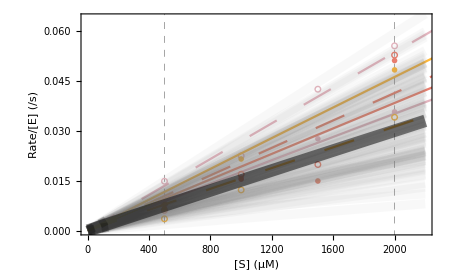
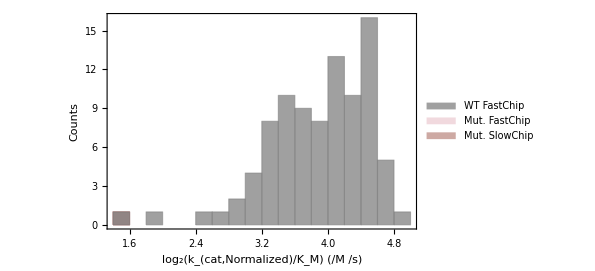
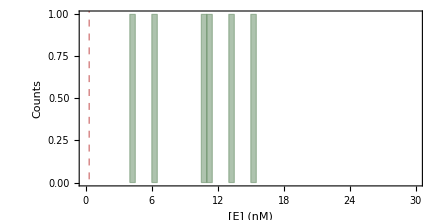
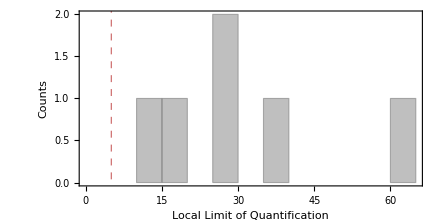
Mutation
-Graphics3D- | Aggregate Parameters
 | Median | StdDev | p-value | n_reps
k_cat/K_M (M^-1 s^-1) | 20.114 | 4.061 | 0.232 | 6
Tier 1 |  |  |  | 
Total Chambers |  |  |  | 6
Expressed (>0.3nM) |  |  |  | 6
LLoD>5&&<6 2pt fits |  |  |  | 7
Tier 2 |  |  |  | 
Total Chambers |  |  |  | N/A
Expressed (>0.3nM) |  |  |  | N/A
LLoD>5&&<6 2pt fits |  |  |  | N/A
Tier 3 |  |  |  | 
Total Chambers |  |  |  | N/A
Expressed (>0.3nM) |  |  |  | N/A
LLoD>5&&<6 2pt fits |  |  |  | N/A | Michaelis-Menten curves
-Graphics-
Michaelis-Menten fit parameters |  | 
 |  | 
-Graphics- | -Graphics- | 
Expression and Limit of Quantification |  | 
 |  | 
-Graphics-

 | -Graphics-
{}
{} | 
Experimental Data |  | 
Experiment | Chip Type | Plot Legend | Column | Row | [E] (nM) | k_cat/K_(M,Norm.) | k_obs | p-value | R^2 | LLoD
180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv | GlyScan | ● -Graphics- | 9 | 3 | 11.01 | 17.783 | 12.495 |  | 1. | 11.8
180531_S2_d1_MecMUP_1_MecMUP_LinComb.csv | GlyScan | ○ -Graphics- | 12 | 27 | 10.78 | 27.096 | 15.762 |  | 0.99 | 25.9
180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv | GlyScan | ● -Graphics- | 12 | 27 | 15.07 | 19.356 | 15.822 |  | 0.88 | 61.4
180509_S3_d1_MecMUP_1_MecMUP_LinComb.csv | GlyScan | ○ -Graphics- | 9 | 3 | 13.31 | 20.872 | 12.27 |  | 0.92 | 29.8
180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv | GlyScan | ● -Graphics- | 9 | 3 | 6.2 | 23.362 | 13.045 |  | 0.99 | 36.3
180513_S3_d1_MecMUP_1_MecMUP_LinComb.csv | GlyScan | ○ -Graphics- | 12 | 27 | 4.26 | 15.789 | 7.146 |  | 0.97 | 16.1
Median k_cat/K_M |  |  |  |  |  | 0 | 12.77 | 0.232 |  | 
 |  |  |  |  |  |  |  |  |  | 
Median WT k_cat/K_M |  |  |  |  |  | 16.217 | 11.178 |  |  |  |  |

```mathematica
Print["Number of mutants with aggregate measurement:"]
Length[total]

datasetIn=Dataset[outForPDF];
(*Export["~/Desktop/PafA_cMUP_aggData_WTR164ANorm_200923.wxf",datasetIn,PerformanceGoal->"Size"]*)

ds2=datasetIn[All,{"MutantID","Experiment","Indices","Column","Row","Data","EnzymeConc","AllSubstrateConcs","AllInitialRates","kcat","kcatNormalized","FitRSquared","BootstrapsFit","kcatCI","KmCI","kcatoverKMCI","kcatNormMean","kcatNormMedian","Km","KmLimit","KmMean","KmMedian","kcat/Km_Norm","kobs","kcat/Km_Norm_Mean","kcat/Km_Norm_Median","kcatNormBootstrapHypothesisTestMedian","KmBootstrapHypothesisTestMedian","kcat/Km_BootstrapHypothesisTestMedian","kcatNormBootstrapHypothesisTestMean","KmBootstrapHypothesisTestMean","kcat/Km_BootstrapHypothesisTestMean"}];

(*Export["~/Desktop/PafA_cMUP_aggData_WTR164ANorm_noPlots.wxf",ds2,PerformanceGoal->"Size"]*)

keys=Keys[forCSV[[1]]]

out2=Prepend[Sort[Flatten[outForCSV,1],ToExpression[StringDrop[StringDrop[#1[[3]],-1],1]]<ToExpression[StringDrop[StringDrop[#2[[3]],-1],1]]&],keys];

(*Export["~/Desktop/PafA_cMUP_aggData_WTR164ANorm_withlowR2.csv",out2,"Data"]*)

dataset=datasetIn[GroupBy["MutantID"]];

m=5;

(*If[m≤Length[total],Grid[{{dataset[m,1,"SummaryTableStructure"],dataset[m,1,"SummaryTableParams"],Column[{Style["Michaelis-Menten curves",Bold],dataset[m,1,"FitPlotNorm"],dataset[m,1,"KmNormPlot"]},Frame->All,Background->{LightGray,None}]},{Style["Michaelis-Menten fit parameters",Bold],SpanFromLeft},{},{dataset[m,1,"kcatNormHistogram"],dataset[m,1,"KmHistogram"],dataset[m,1,"kcat/Km_Histogram"]},{dataset[m,1,"ReplicatePlot"],dataset[m,1,"ReplicatePlotKm"],dataset[m,1,"kcatvsKmPlot"]},{Style["Expression and Limit of Quantification",Bold],SpanFromLeft},{},{dataset[m,1,"ExpressionHist"],dataset[m,1,"FractionCulledHist"]},{Style["Experimental Data",Bold],SpanFromLeft},{Grid[Normal[dataset[m,1,"DataTable"]],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}],SpanFromLeft}},Frame->True,Dividers->{{True,False,False,True,False,True,True,True},{True,True}},Background->{{None,None},{None,LightGray,None,None,None,LightGray,None,None,LightGray}},Alignment->Top,Spacings->2],Grid[{{Column[{dataset[m,1,"SummaryTableStructure"],Grid[{{Style["Expression",Bold]},{},{dataset[m,1,"ExpressionHist"]}},Frame->True,Dividers->{{True,True,False},{True,True}},Background->{{None,None},{LightGray,None}},Alignment->Top]}],Column[{dataset[m,1,"SummaryTableParams"],Grid[{{Style["Limit of Quantification",Bold]},{},{dataset[m,1,"FractionCulledHist"]}},Frame->True,Dividers->{{True,True,False},{True,True}},Background->{{None,None},{LightGray,None}},Alignment->Top]}],Grid[Normal[dataset[m,1,"DataTable"]],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}]},{"",""}},Alignment->Top]]*)

If[m≤Length[total],Grid[{{dataset[m,1,"SummaryTableStructure"],dataset[m,1,"SummaryTableParams"],Column[{Style["Michaelis-Menten curves",Bold],dataset[m,1,"FitPlotNorm"]},Frame->All,Background->{LightGray,None}]},{Style["Michaelis-Menten fit parameters",Bold],SpanFromLeft},{},{dataset[m,1,"kcat/Km_Histogram"],dataset[m,1,"ReplicatePlot"]},{Style["Expression and Limit of Quantification",Bold],SpanFromLeft},{},{dataset[m,1,"ExpressionHist"],dataset[m,1,"FractionCulledHist"]},{Style["Experimental Data",Bold],SpanFromLeft},{Grid[Normal[dataset[m,1,"DataTable"]],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}],SpanFromLeft}},Frame->True,Dividers->{{True,False,False,True,False,True,True,True},{True,True}},Background->{{None,None},{None,LightGray,None,None,None,LightGray,None,None,None,LightGray}},Alignment->Top,Spacings->2],Grid[{{Column[{dataset[m,1,"SummaryTableStructure"],Grid[{{Style["Expression",Bold]},{},{dataset[m,1,"ExpressionHist"]}},Frame->True,Dividers->{{True,True,False},{True,True}},Background->{{None,None},{LightGray,None}},Alignment->Top]}],Column[{dataset[m,1,"SummaryTableParams"],Grid[{{Style["Limit of Quantification",Bold]},{},{dataset[m,1,"FractionCulledHist"]}},Frame->True,Dividers->{{True,True,False},{True,True}},Background->{{None,None},{LightGray,None}},Alignment->Top]}]},{Grid[Normal[dataset[m,1,"DataTable"]],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{LightGray,None},{LightGray,None}}],SpanFromLeft},{"",""}},Alignment->Top]]
```

```mathematica
maxExponent=Round[Log[10,$MaxMachineNumber]]+1;

testF2[in_]:=Which[NumberQ[in],ToString[NumberForm[in,ScientificNotationThreshold->{-maxExponent,maxExponent}]],ListQ[in],ToString[NumberForm[#,ScientificNotationThreshold->{-maxExponent,maxExponent}]&/@in],NumberQ[in]==False&&ListQ[in]==False,in]
```

```mathematica
keys=Keys[forCSV[[1]]]

out2=Prepend[Sort[Flatten[outForCSV,1],ToExpression[StringDrop[StringDrop[#1[[3]],-1],1]]<ToExpression[StringDrop[StringDrop[#2[[3]],-1],1]]&],keys];

Export["~/Desktop/PafA_MecMUP_aggData_WTNorm_v.2.0_201008.csv",Prepend[Map[testF2,Flatten[outForCSV,1],{2}],keys]]
```

{Version,RunDate,MutantID,Experiment,ChipType,Column,Row,EnzymeConc,AllSubstrateConcs,AllInitialRates,kcat,kcatNormalized,kcatLimit,KMFit,KMLimitValue,KMLimit,kcat/KMFit,FitRSquared,kcatFitError,KMFitError,kcatoverKMFitError,kcatNormMean,kcatNormMedian,KMMean,KMMedian,kcat/KMNorm,kobsRaw,kobsNegCorrected,kcat/KMNormMean,kcat/KMNormMedian,kcatNormBootstrapHypothesisTestMedian,KMBootstrapHypothesisTestMedian,kcat/KMBootstrapHypothesisTestMedian,kobsBootstrapHypothesisTestMedian,Log2StdDevkcat,Log2StdDevKM,Log2StdDevkcat/KM,Log2StdDevkcat/KMLimit,kcatNormBootstrapHypothesisTestMean,KMBootstrapHypothesisTestMean,kcat/KMBootstrapHypothesisTestMean,kobsBootstrapHypothesisTestMean,NumCulledReps,LBR,ContaminantRatio,StdDevkcat,StdDevKM,StdDevkcat/KM,kcat/KMLimit,kcatAggLimit,KMAggLimit,kcat/KMAggLimit,KMMedianLimit,KMMeanLimit,kcat/KMNormMedianLimit,kcat/KMNormMeanLimit}

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

~/Desktop/PafA_MecMUP_aggData_WTNorm_v.2.0_201008.csv